```mathematica
2-2
```

0

# Resistors in Uniform Cubic Array

## Two Uncommon Approaches to Solution of a Classic DC Circuit Problem

Nicholas Wheeler
28 September 2011

### Introduction

Twelve resistors are connected in cubic array:

-Graphics3D-

The following undirected graph

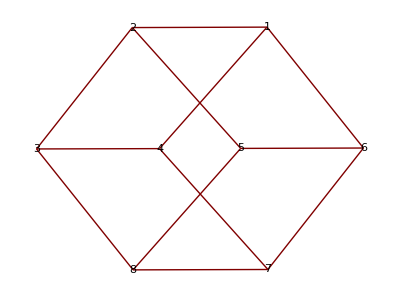

will serve to assign identifying numbers to the eight nodal junctions: it is simply as a matter of style—and of no real consequence—that I have arranged for the numbers assigned to diametrically opposite nodes sum in every instance to 9. It will be assumed initially that a current J enters the circuit at the high-potental node #1, exits at the low-potential (grounded) diametric node #8. 

PROBLEM: Find (1) the current in every resistive edge) and (2) the potential differences between every pair of nodes, given either the through-current J or the impressed potential V. 

There are, we note,  a total of

```mathematica
1+2+3+4+5+6+7==Binomial[8,2]==28
```

True

such nodal pairs, but those potential differences are all latent in the eight nodal potentials relative to ground.

If we proposed to approach the problem by textbook appeal to 
 
  • Kirchhoff's nodal rule (conservation of charge);
  • Kirchhoff's loop rule (static E-fields are conservative: ∮  E • ds = 0);
  • Ohm's Law
  
we would standardly begin by arbitrarily assigning directionality to the current flow through each resistor, which is to say: we would work from an arbitrarily directed graph:

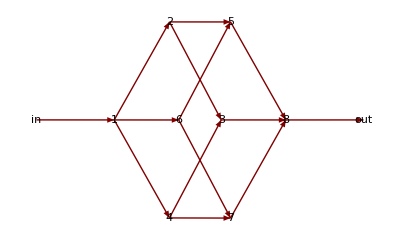

REMARK: In the figure I have looked to physical intuition for my directionality assignments.

The textbook approach leads (because, according to Ohm, resistors are linear devices) to a readily soluable system of 2N simultaneous linear equations, but suffers from this defect: there is—except in the simplest cases—no "most natural" way to select N independent loops from the very large (how large?) set of all possible loops. Every such selection is, to some (typically very large) degree, arbitrary, and tends therefore to conceal (i.e., to fail to transparently reflect) the overall structure of the circuit. 

I will describe two alternative ways to approach such problems, both of which are free of the defect just mentioned:

VARIATIONAL METHOD: Implementation of the claim that the physically realized branch currents are those which (subject always to the constraints implicit in Kirchhoff's nodal rule) minimize the rate of energy dissipation.

MONTE CARLO METHOD: Exploits the discovery that the DC circuit problem is mathematically equivalent to a problem involving random walks of the circuit graph.

Both methods provide ways—complementary ways—to gain direct insight into DC circuit physics. The situation here—at least so far as concerns the Variational Method—will be somewhat reminiscent of that posed by problems in mechanics, where "energetic considerations" are often more informative (speak more immediately to physical intuition) than are the laboriously constructed explicit solutions of the equations of motion.

I will, in the present Notebook, illustrate those methods as they pertain only to the classic unit cubic circuit (12 resistors, all of unit value), and will be content to execute certain constructions "by hand." In a companion Notebook I will consider generalizations of the problem, and will be at pains to indicate how Mathematica can be commanded to "automate" those constructions.

### Use of SYMMETRY ARGUMENTS to solve the uniform cubic circuit problem

It is clear by inspection

-Graphics3D-

that  J_blue=1/3 J,  J_red=1/6 J.  As one advances blue-red-blue from the entry node to the exit node one encounters (on the assumption that all resistors have value R) successive potential drops 1/3 JR, 1/6 JR and 1/3 JR, so if V is the potential difference between the entry/exit nodes we have

V=5/6 R J

and the effective resistance of the array becomes

R_effective=5/6 R

The simplicity of the argument owes everything to the symmetry of the array, and would be lost if (1) we assigned unequal values to the resistors, or (2) adopted non-diametric entry/exit nodes.

### Introduction to the VARIATIONAL METHOD

It has always seemed to me to be self-evident that current passing through a resistive DC network will be so partitioned as to minimize the dissipation rate. I have never attempted to construct a formal proof of that proposition (though have frequently asked students to demonstrate its validity in simple cases: two resistors in parallel, the Wheatstone bridge). It is a proposition which I have assumed to be well known to electrical engineers, and am surprised to discover that as recently as 1999 it was presented in the pages of the American Journal of Physics (D. A. Van Baak, "Variational alternatives to Kirchhoff's loop theorem in dc circuits," AJP 67, 36 (1999)) as something of a novelty. Van Bank does provide, in his Section III, an elaborate "Proof of the Variational Principle," and traces its ancestory all the way back to Maxwell, who in A Treatise on Electricity & Magnetism §§ 283-284 proves that

"In any system of conductors in which there are no internal electromotive forces the heat generated by currents distributed in    accordance with Ohm's Law is less than if the currents had been distributed in any other manner consistent with the actual conditions of supply and outflow of the current."

Van Baak also cites a comment added by J. J. Thomson as a footnote to Maxwell's §283 when he edited the posthumous 2^nd edition of Maxwell's treatisem and §358 in the 5^thedition of J. Jeans'  The Mathematical Theory of Electricity & Magnetism, where the subject is revisited.  In the Note which Feynman appended to Chapter 19, "The Principle of Least Action" (Vol. 2 of The Feynman Lectures on Physics) he expresses deep interest in the subject—which had only recently come to his attention— and in its entropic and unresolved quantum mechanical underpinnings. Feynman notes that we have here an instance of a variational principle which does not trace back ultimately to the mechanical principle of least action.
 
Here I am content to accept the validity of that variational principle as a given.

#### Current labeling convention

I will write

J_(m,n) to indicate the current m ⟶ n

as indicated in the following figure:

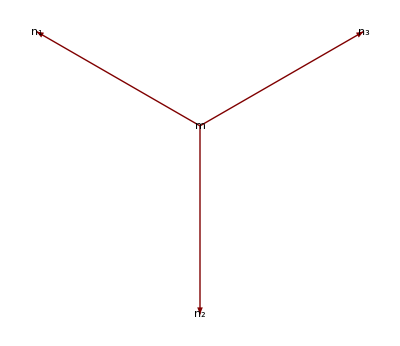

```mathematica
GraphPlot[{m->Subscript[n, 1],m->Subscript[n, 2],m->Subscript[n, 3]}, VertexLabeling->True,DirectedEdges->True]
```

Evidently

J_(m,n)=-J_(n,m)
J_(m,m)=0

which is to say: the "current matrix" 𝕁 is antisymmetric.

Reading from the diagram

-Graphics-

we see that the currents of interest in cubic array problems (apart from the entry and exit currents J) are

```mathematica
CubicCurrents={Subscript[J, 1,2],Subscript[J, 1,4],Subscript[J, 1,6],Subscript[J, 2,3],Subscript[J, 2,5],Subscript[J, 4,7],Subscript[J, 4,3],Subscript[J, 6,5],Subscript[J, 6,7],Subscript[J, 3,8],Subscript[J, 5,8],Subscript[J, 7,8]};
```

#### Nodal constraints

Reading again from the figure, we find—this is the kind of tedious work that, when we turn to DC-circuits-in-general, we will want to automate—that our 12 unknown edge currents are subject (Kirchhoff's node rule) to these 8 constraints:

```mathematica
Subscript[J, 1,2]+Subscript[J, 1,4]+Subscript[J, 1,6]-1==0
-Subscript[J, 1,2]+Subscript[J, 2,3]+Subscript[J, 2,5]==0
-Subscript[J, 2,3]-Subscript[J, 4,3]+Subscript[J, 3,8]==0
-Subscript[J, 1,4]+Subscript[J, 4,3]+Subscript[J, 4,7]==0
-Subscript[J, 2,5]-Subscript[J, 6,5]+Subscript[J, 5,8]==0
-Subscript[J, 1,6]+Subscript[J, 6,5]+Subscript[J, 6,7]==0
-Subscript[J, 4,7]-Subscript[J, 6,7]+Subscript[J, 7,8]==0
-Subscript[J, 3,8]-Subscript[J, 5,8]-Subscript[J, 7,8]+1==0
```

REMARK: It is because we are about to ask Mathematica to perform a calculation which it is ill-equipped to perform symbolically that I have at this point assigned a specific numerical value J = 1 to the through-current.

It is for the convenience of Mathematica that we give those eight equations a collective name:

```mathematica
NodalConstraints={Subscript[J, 1,2]+Subscript[J, 1,4]+Subscript[J, 1,6]-1==0,
-Subscript[J, 1,2]+Subscript[J, 2,3]+Subscript[J, 2,5]==0,
-Subscript[J, 2,3]-Subscript[J, 4,3]+Subscript[J, 3,8]==0,
-Subscript[J, 1,4]+Subscript[J, 4,3]+Subscript[J, 4,7]==0,
-Subscript[J, 2,5]-Subscript[J, 6,5]+Subscript[J, 5,8]==0,
-Subscript[J, 1,6]+Subscript[J, 6,5]+Subscript[J, 6,7]==0,
-Subscript[J, 4,7]-Subscript[J, 6,7]+Subscript[J, 7,8]==0,
-Subscript[J, 3,8]-Subscript[J, 5,8]-Subscript[J, 7,8]+1==0};
```

#### Calculating the minimal dissipation rate

The dissipation function for our uniform cube (all resistances set equal to unity) reads

```mathematica
DissipationFunction=Subscript[J, 1,2]^2+Subscript[J, 1,4]^2+Subscript[J, 1,6]^2+Subscript[J, 2,3]^2+Subscript[J, 2,5]^2+Subscript[J, 4,7]^2+Subscript[J, 4,3]^2+Subscript[J, 6,5]^2+Subscript[J, 6,7]^2+Subscript[J, 3,8]^2+Subscript[J, 5,8]^2+Subscript[J, 7,8]^2;
```

which, we observe, describes a sphere of radius √DissipationFunction in 12-dimensional J-space.

We are in position now to command

```mathematica
Minimize[Flatten[{DissipationFunction, NodalConstraints}],CubicCurrents]
```

{5/6,{J_(1,2)→1/3,J_(1,4)→1/3,J_(1,6)→1/3,J_(2,3)→1/6,J_(2,5)→1/6,J_(4,7)→1/6,J_(4,3)→1/6,J_(6,5)→1/6,J_(6,7)→1/6,J_(3,8)→1/3,J_(5,8)→1/3,J_(7,8)→1/3}}

These results

{J_(1,2)→1/3,J_(1,4)→1/3,J_(1,6)→1/3,J_(3,8)→1/3,J_(5,8)→1/3,J_(7,8)→1/3}
{J_(2,3)→1/6,J_(2,5)→1/6,J_(4,7)→1/6,J_(4,3)→1/6,J_(6,5)→1/6,J_(6,7)→1/6}

agree precisely with the results obtained previously by the classic symmetry argument. From

DissipationRate=R_effective J^2
V=R_effective J

and J = 1 we obtain

DissipationRate=V=R_effective=5/6

which also agrees with a result of the symmetry argument.

#### Calculating the nodal potentials

Generally, if

V_m = potential of m^th node, relative to ground

then V_m-V_n=R_(m,n)J_(m,n). In the present instance (since all resistances are unity, node #8 is grounded, and the potential at node #1 has been established to be 5/6) we have

```mathematica
Subscript[V, 1]=5/6;
Subscript[V, 8]=0;
```

```mathematica
NodalPotentials={
Subscript[V, 1]-Subscript[V, 2]==1/3,
Subscript[V, 1]-Subscript[V, 4]==1/3,
Subscript[V, 1]-Subscript[V, 6]==1/3,
Subscript[V, 3]-Subscript[V, 8]==1/3,
Subscript[V, 5]-Subscript[V, 8]==1/3,
Subscript[V, 7]-Subscript[V, 8]==1/3,
Subscript[V, 2]-Subscript[V, 5]==1/6,
Subscript[V, 6]-Subscript[V, 5]==1/6,
Subscript[V, 6]-Subscript[V, 7]==1/6,
Subscript[V, 4]-Subscript[V, 7]==1/6,
Subscript[V, 4]-Subscript[V, 3]==1/6,
Subscript[V, 2]-Subscript[V, 3]==1/6}
```

{5/6-V_2==1/3,5/6-V_4==1/3,5/6-V_6==1/3,V_3==1/3,V_5==1/3,V_7==1/3,V_2-V_5==1/6,-V_5+V_6==1/6,V_6-V_7==1/6,V_4-V_7==1/6,-V_3+V_4==1/6,V_2-V_3==1/6}

```mathematica
Solve[%,{Subscript[V, 2],Subscript[V, 3],Subscript[V, 4],Subscript[V, 5],Subscript[V, 6],Subscript[V, 7]}]
```

{{V_2→1/2,V_3→1/3,V_4→1/2,V_5→1/3,V_6→1/2,V_7→1/3}}

The statements

V_1=5/6
V_2=V_4=V_6=1/2
V_3=V_5=V_7=1/3
v_0=0

—of which this provides a diagramatic representation

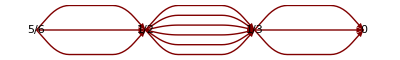

```mathematica
GraphPlot[{5/6->1/2,5/6->1/2,5/6->1/2,1/2->1/3,1/2->1/3,1/2->1/3,1/2->1/3,1/2->1/3,1/2->1/3,1/3->0,1/3->0,1/3->0},DirectedEdges->True, VertexLabeling->True,AspectRatio->.15]
```

—are again in precise agreement with results of the symmetry argument. These results are easily seen to be in conformity with Kirchhoff's loop rule, but nowhere did we draw upon that rule.

#### Effect of changing the relative placement of the electrodes

There are—because of the symmetry of the array—only two cases to consider: the electrodes, instead of being diametric, can be (1) next-to-adjacent or (2) adjacent. In both of the latter cases the symmetry argument becomes inapplicable (and beyond salvation), but the variational method requires only the slightest of adjustment:

NEXT-TO-ADJACENT ELECTRODES:

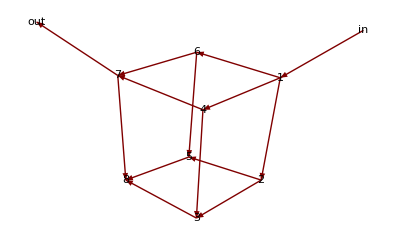

We adjust the nodal constraints

```mathematica
NodalConstraints2={Subscript[J, 1,2]+Subscript[J, 1,4]+Subscript[J, 1,6]-1==0,
-Subscript[J, 1,2]+Subscript[J, 2,3]+Subscript[J, 2,5]==0,
-Subscript[J, 2,3]-Subscript[J, 4,3]+Subscript[J, 3,8]==0,
-Subscript[J, 1,4]+Subscript[J, 4,3]+Subscript[J, 4,7]==0,
-Subscript[J, 2,5]-Subscript[J, 6,5]+Subscript[J, 5,8]==0,
-Subscript[J, 1,6]+Subscript[J, 6,5]+Subscript[J, 6,7]==0,
-Subscript[J, 4,7]-Subscript[J, 6,7]+Subscript[J, 7,8]+1==0,
-Subscript[J, 3,8]-Subscript[J, 5,8]-Subscript[J, 7,8]==0};
```

and immediately obtain

```mathematica
Minimize[Flatten[{DissipationFunction, NodalConstraints2}],CubicCurrents]
```

{3/4,{J_(1,2)→1/4,J_(1,4)→3/8,J_(1,6)→3/8,J_(2,3)→1/8,J_(2,5)→1/8,J_(4,7)→3/8,J_(4,3)→0,J_(6,5)→0,J_(6,7)→3/8,J_(3,8)→1/8,J_(5,8)→1/8,J_(7,8)→-1/4}}

Note that the effective resistance has (as we intuitively expect) been reduced, from 10/12 to 9/12. And that one of the currents has now reversed direction.

ADJACENT ELECTRODES:

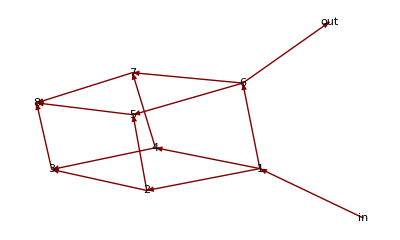

Again adjusting the constraints

```mathematica
NodalConstraints3={Subscript[J, 1,2]+Subscript[J, 1,4]+Subscript[J, 1,6]-1==0,
-Subscript[J, 1,2]+Subscript[J, 2,3]+Subscript[J, 2,5]==0,
-Subscript[J, 2,3]-Subscript[J, 4,3]+Subscript[J, 3,8]==0,
-Subscript[J, 1,4]+Subscript[J, 4,3]+Subscript[J, 4,7]==0,
-Subscript[J, 2,5]-Subscript[J, 6,5]+Subscript[J, 5,8]==0,
-Subscript[J, 1,6]+Subscript[J, 6,5]+Subscript[J, 6,7]+1==0,
-Subscript[J, 4,7]-Subscript[J, 6,7]+Subscript[J, 7,8]==0,
-Subscript[J, 3,8]-Subscript[J, 5,8]-Subscript[J, 7,8]==0};
```

we command

```mathematica
Minimize[Flatten[{DissipationFunction, NodalConstraints3}],CubicCurrents]
```

{7/12,{J_(1,2)→5/24,J_(1,4)→5/24,J_(1,6)→7/12,J_(2,3)→1/24,J_(2,5)→1/6,J_(4,7)→1/6,J_(4,3)→1/24,J_(6,5)→-5/24,J_(6,7)→-5/24,J_(3,8)→1/12,J_(5,8)→-1/24,J_(7,8)→-1/24}}

and find that the effective resistance has been further reduced, from 9/12 to 7/12. And that another three currents have reversed direction.

### Introduction to the MONTE CARLO METHOD

It was from a reading of Chapter 17 in Paul J. Nahin's Mrs. Perkins's Electric Quilt, and Other Intriguing Stories of Mathematical Physics (Princeton UP, 2009) that this method came first to my attention. The subject has come up only a few times in the pages of AJP (see, for example, Raymond A. Sorensen, "The random walk method for dc circuit analysis," AJP 58, 1056-1059 (1990)) and the principal source, all authors seem to agree, is Peter G. Doyle & J. Laurie Snell, Random Walks and Electrical Networks (published in 1984 as an American Mathematical Association Carus Monograph, now available as a free download in a 2006 version). According to those authors, the first hint of the possibility of such an application of the theory of random walks can be found in S. Kakutani, "Markov processes and the Dirichlet problem," Proc. Jap. Acad. 21, 227-233 (1945). I gather from having Googled the web that random walk techniques are now widely used by engineers concerned with power grid analysis, the behavior of circuits with millions of components, etc. But every source that I have managed thus far to consult has seemed to me to be disappointing in one respect or another. In what follows my principal debt has been to Nahin, but my objective is different from his: I seek to show how Mathematica-based techniques can be used actually to apply the Monte Carlo technique, and to gain some sense of the reliability of the results that can be thus achieved.

#### Foundations

Kirchhoff's node rule can be formulated

∑_(n∈N[m]) J_(m,n)=0

where

N[m] denotes the set of nodes adjacent to Node m

To say the same thing another way (appealing here to Ohm's Law),

∑_(n∈N[m]) (V_m-V_n)/R_mn=0

or (replacing the resistances by the associated conductances C_mn=R_mn^-1)

∑_(n∈N[m]) C_mn(V_m-V_n)=0

whence

V_m=∑_(n∈N[m]) C_mn/C_m V_n    where    C_m=  ∑_(n∈N[m]) C_mn

Evidently C_mn/C_m measures "fractional conductance," and

∑_(n∈N[m]) C_mn/C_m=1

Consider now a guy ("electron") who walks randomly on the graph that represents the design of the circuit. Let

p_(m,n) = probability that,if at Node m,his next step takes him to adjacent Node n

Select two nodes that we agree to call n_A and n_B (or sometimes simply A and B), respectively. Let

P_m= probability of walking m ⟶ A without visiting B

Clearly

P_A=1
P_B=0

and

P_m=∑_(n∈N[m]) p_(m,n)P_n

The Monte Carlo approach to DC circuit analysis hinges on the observation that if we set the transition probablities equal to the fractional conductances

p_(m,n)=C_mn/C_m

—which, if our walker is an "electron," seems eminently sensible—then the red equations become identical: the nodal probablities P_m become interpretable as nodal potentials (relative to the grounded node B, the potential at node A being assumed without loss of generality to be unity).

#### Preparatory general remarks about random walks on graphs

A walker who departs from a specified node on (let us say) an 8-node graph can, after an n-step walk, find himself standing on any one of a variety of nodes. We write

(p_1
p_2
p_3
⋮
p_8)_n

to describe the probability (relative frequency in an indefinitely large population of such walks) that he finds himself on this node or that. We will refer to such stochastic vectors (vectors with elements drawn from the unit interval, which sum to unity) "state vectors," though there refer to the "state of our expectations," not to the momentary state of any individual walker. 

One step later, we have

(p_1
p_2
p_3
⋮
p_8)_(n+1)=(p_(1,1) | p_(1,2) | p_(1,3) | ⋯ | p_(1,8)
p_(2,1) | p_(2,2) | p_(2,3) | ⋯ | p_(2,8)
p_(3,1) | p_(3,2) | p_(3,3) | ⋯ | p_(3,8)
⋮ | ⋮ | ⋮ | ⋱ | ⋮
p_(8,1) | p_(8,2) | p_(8,3) | ⋯ | p_(8,8))(p_1
p_2
p_3
⋮
p_8)_n

where

p_(m,n)=probability of transition m ⟵ n

and the square matrix 𝕋 will be called the "transition matrix." Such matrices (also called "Markov matrices") are distinguished from square-matrices-in-general by the circumstances that (1) all elements are drawn from the unit interval, and (2) the elements in any column sum to unity.  

In a special class of cases 𝕋 is symmetric, meaning

p_(m,n)=p_(n,m)   :   all m and n

The principle of detailed balance is operative in such cases. The DC circuit application will present us with 𝕋-matrices that are typically asymmetric, and the principle of detailed balance is typically not operative.

If (as was tacitly assumed above) the walker makes his next-step decision with full knowledge of where he momentarily is but with no recollection of where he previously was (if he is, in short, "memoriless"), if he bases his next-step decision upon information written into the structure of a 𝕋-matrix that remains ever constant, then his random walk provides an instance of a "Markov process." 

All information having to do with the evolution of state vectors  can be extracted from the spectral properties of 𝕋-matrices: that is a pretty subject, but I will postpone discussion of its principal features until we have specific need of them.

The DC circuit application asks us to look to individual walks, and to resolve them into two classes, according as they do or do not possess a certain property. To that end we will have to unpack and to reassemble the information written into 𝕋.

#### Preparing to generate individual random walks on a uniform cubic array

From the graph of the cubic array (pay no attention for the moment to the "in"/"out" details)

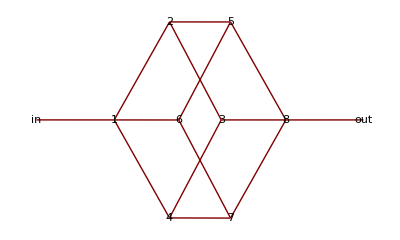

we read off the associated/equivalent "adjacency matrix"

```mathematica
𝔸=({{0, 1, 0, 1, 0, 1, 0, 0}, {1, 0, 1, 0, 1, 0, 0, 0}, {0, 1, 0, 1, 0, 0, 0, 1}, {1, 0, 1, 0, 0, 0, 1, 0}, {0, 1, 0, 0, 0, 1, 0, 1}, {1, 0, 0, 0, 1, 0, 1, 0}, {0, 0, 0, 1, 0, 1, 0, 1}, {0, 0, 1, 0, 1, 0, 1, 0}})
```

Note the symmetry if 𝔸, which reflects the fact that

A adjacent to B  ⟺ B adjacent to A

The "resistance matrix" is a weighted version of the adjacency matrix, that indicates not only how the resistors are connected but also their individual values R_mn. For the uniform cube (all resistors are unit resistors) we have

```mathematica
ℝ=({{∞, 1, ∞, 1, ∞, 1, ∞, ∞}, {1, ∞, 1, ∞, 1, ∞, ∞, ∞}, {∞, 1, ∞, 1, ∞, ∞, ∞, 1}, {1, ∞, 1, ∞, ∞, ∞, 1, ∞}, {∞, 1, ∞, ∞, ∞, 1, ∞, 1}, {1, ∞, ∞, ∞, 1, ∞, 1, ∞}, {∞, ∞, ∞, 1, ∞, 1, ∞, 1}, {∞, ∞, 1, ∞, 1, ∞, 1, ∞}})
```

where ∞ records the fact that open circuits (absent wires) conduct no current because (formally, at least) they have infinite resistance.  The associated "conductance matrix" is the matrix of reciprocals (not to be confused with the inverse of the matrix!)

```mathematica
ℂ=({{∞, 1, ∞, 1, ∞, 1, ∞, ∞}, {1, ∞, 1, ∞, 1, ∞, ∞, ∞}, {∞, 1, ∞, 1, ∞, ∞, ∞, 1}, {1, ∞, 1, ∞, ∞, ∞, 1, ∞}, {∞, 1, ∞, ∞, ∞, 1, ∞, 1}, {1, ∞, ∞, ∞, 1, ∞, 1, ∞}, {∞, ∞, ∞, 1, ∞, 1, ∞, 1}, {∞, ∞, 1, ∞, 1, ∞, 1, ∞}})^-1;
ℂ//MatrixForm
```

(0 | 1 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0)

The symmetry of ℂ is typical, but that it simply reproduces 𝔸 reflects the fact thatwe have allowed ourselves to use only unit resistors.

Drawing now upon the principle that transition probabilities are to be identified with fractional conductances p_(m,n)=C_mn/C_m, we obtain the transition matrix that regulates random walks on the unit cubic array:

```mathematica
𝕋=({{0, 1/3, 0, 1/3, 0, 1/3, 0, 0}, {1/3, 0, 1/3, 0, 1/3, 0, 0, 0}, {0, 1/3, 0, 1/3, 0, 0, 0, 1/3}, {1/3, 0, 1/3, 0, 0, 0, 1/3, 0}, {0, 1/3, 0, 0, 0, 1/3, 0, 1/3}, {1/3, 0, 0, 0, 1/3, 0, 1/3, 0}, {0, 0, 0, 1/3, 0, 1/3, 0, 1/3}, {0, 0, 1/3, 0, 1/3, 0, 1/3, 0}});
```

The symmetry of this 𝕋-matrix (which describes a balanced Markov process) is atypical: it reflects that we are considering a physical array in which all conductances are equal. 

Note the zeros on the principal diagonal

p_(m,m)=0    :    all m

which say: "Keep moving; no lingering allowed." This is a feature shared by all the 𝕋 matrices that arise from DC circuit problems: it reflects that fact that C_mm= 0 (all m): no wires link nodes to themselves.

#### Generation of individual random walks on a uniform cubic array

The momentary state of an individual walker is described always by one or another of the row vectors σ_k that are constructed by the following command

```mathematica
Table[Subscript[σ, k]=Table[KroneckerDelta[j,k],{j,1,8}],{k,1,8}]
```

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

and which, when displayed as column vectors (trivial stochastic vectors) look like this:

```mathematica
Table[MatrixForm[Transpose[{Subscript[σ, k]}]],{k,1,8}]
```

{(1
0
0
0
0
0
0
0),(0
1
0
0
0
0
0
0),(0
0
1
0
0
0
0
0),(0
0
0
1
0
0
0
0),(0
0
0
0
1
0
0
0),(0
0
0
0
0
1
0
0),(0
0
0
0
0
0
1
0),(0
0
0
0
0
0
0
1)}

REMARK: Column vectors fall most familiarly upon the eye, but for computational convenience and economy of display I from this point forward I elect to work with row vectors.

The walker—before he can figure out the nest-step options available to him—must first discover the identity of the node on which he presently stands. If he finds himself to be standing on the j^th node he then looks to the transition probabilities recorded in the j^th column (or in the present instance—by symmetry—the j^th row) and makes a random choice based upon those probabilities. To orchestrate that decision process, we give names to the respective columns/rows of 𝕋

```mathematica
Table[Subscript[T, k]=𝕋⟦k⟧,{k,1,8}];
```

```mathematica
Table[Subscript[T, k],{k,1,8}]//TableForm
```

0 | 1/3 | 0 | 1/3 | 0 | 1/3 | 0 | 0
1/3 | 0 | 1/3 | 0 | 1/3 | 0 | 0 | 0
0 | 1/3 | 0 | 1/3 | 0 | 0 | 0 | 1/3
1/3 | 0 | 1/3 | 0 | 0 | 0 | 1/3 | 0
0 | 1/3 | 0 | 0 | 0 | 1/3 | 0 | 1/3
1/3 | 0 | 0 | 0 | 1/3 | 0 | 1/3 | 0
0 | 0 | 0 | 1/3 | 0 | 1/3 | 0 | 1/3
0 | 0 | 1/3 | 0 | 1/3 | 0 | 1/3 | 0

and—to construct "by hand" an illustrative 5-step random walk that begins with the walker standing on (say) Node #3—command

```mathematica
Subscript[σ, 3]
RandomChoice[Sum[%⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4],Subscript[σ, 5],Subscript[σ, 6],Subscript[σ, 7],Subscript[σ, 8]},1]⟦1⟧
RandomChoice[Sum[%⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4],Subscript[σ, 5],Subscript[σ, 6],Subscript[σ, 7],Subscript[σ, 8]},1]⟦1⟧
RandomChoice[Sum[%⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4],Subscript[σ, 5],Subscript[σ, 6],Subscript[σ, 7],Subscript[σ, 8]},1]⟦1⟧
RandomChoice[Sum[%⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4],Subscript[σ, 5],Subscript[σ, 6],Subscript[σ, 7],Subscript[σ, 8]},1]⟦1⟧
RandomChoice[Sum[%⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4],Subscript[σ, 5],Subscript[σ, 6],Subscript[σ, 7],Subscript[σ, 8]},1]⟦1⟧
```

{0,0,1,0,0,0,0,0}

{0,0,0,0,0,0,0,1}

{0,0,0,0,0,0,1,0}

{0,0,0,0,0,1,0,0}

{1,0,0,0,0,0,0,0}

{0,1,0,0,0,0,0,0}

Repeat the command to generate a different walk. Notice that the walker does in fact never linger.

If, however, we have interest in long walks then that "by hand" procedure becomes excessively tedious; we need an automated procedure. This works, as I demonstrate by generation of a typical 10-step walk :

```mathematica
NestList[RandomChoice[Sum[#⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4],Subscript[σ, 5],Subscript[σ, 6],Subscript[σ, 7],Subscript[σ, 8]},1]⟦1⟧&,Subscript[σ, 3],10]//TableForm
```

0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0

Monte Carlo methods—to whatever end they are applied—require access to large populations of walks. The following command generates a 6-member population of 10-step walks, all of which take Node #3 as the point of departure:

```mathematica
Six10StepWalks=Table[NestList[RandomChoice[Sum[#⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4],Subscript[σ, 5],Subscript[σ, 6],Subscript[σ, 7],Subscript[σ, 8]},1]⟦1⟧&,Subscript[σ, 3],10],{j,1,6}];

Table[TableForm[Six10StepWalks⟦k⟧],{k,1,6}]
```

{0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0,0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0,0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0,0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0,0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0,0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0}

DIGRESSION: By looking to the last-state statistics of a much larger population of such walks one should be able to construct "experimental estimates" of the data written into the stochastic vector generated by the following command:

```mathematica
MatrixForm[MatrixPower[𝕋,10].({{0}, {0}, {1}, {0}, {0}, {0}, {0}, {0}})]//N
```

(0.249996
0.
0.250013
0.
0.249996
0.
0.249996
0.)

but I have other fish to fry, so will not linger to do so. The latter result does, however, hint at a curious fact to discussion of which I do promise ultimately to return. END OF DIGRESSION

#### Finally: Monte Carlo estimation of the nodal potentials

Looking again to the layout of the uniform cubic array

-Graphics-

we assume the potential at the input node

A={1,0,0,0,0,0,0}

is V = 1, and at the (grounded) output node is

B={0,0,0,0,0,0,1}

We seek the potentials at the 6 remaining nodes, but it was previous observed that (by symmetry) V_2=V_4=V_6 and V_7=V_5=V_3 so we really have only two cases to consider. Accordingly, we launch the walker ("electron") from

C={0,1,0,0,0,0,0,0}

and ask for an estimate of the probability that he (it) successfully reaches A without having visited B, or we launch him from

D={0,0,1,0,0,0,0,0}

and ask the same thing.

As a first step toward that objective, I construct a command that generates (here—initially—a short list of 50) named walks that automatically stop upon first arrival at A:

```mathematica
Table[{Subscript[Walk, n]=NestWhileList[RandomChoice[Sum[#⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4],Subscript[σ, 5],Subscript[σ, 6],Subscript[σ, 7],Subscript[σ, 8]},1]⟦1⟧&,Subscript[σ, 2],#≠{1,0,0,0,0,0,0,0}&]},{n,1,50}];
```

Here is a 10-member sample of the walks thus generated. Notice that some are short, some are long; each begins at C and ends at A; some visit B one or more times en route to A, while some successfully avoid B:

```mathematica
Table[{j,Subscript[Walk, j]},{j,15,25}]//TableForm
```

15 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
17 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
18 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
19 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
20 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
21 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
22 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
23 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
24 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
25 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0

The idea now is to examine the walks, one at a time, and to print A if the 1 s in the 8^th place sum to 0—signifying that B has been successfully avoided—and in all other cases to print B. Here are illustrative instances of a command that is seen by inspection to accomplish that objective :

```mathematica
Table[Which[Sum[Subscript[Walk, j]⟦k⟧⟦8⟧,{k,1,Length[Subscript[Walk, j]]}]==0,A,Sum[Subscript[Walk, j]⟦k⟧⟦8⟧,{k,1,Length[Subscript[Walk, j]]}]!=0,B],{j,1,50}]
```

{A,A,B,A,A,B,A,A,B,B,B,A,B,B,B,A,A,A,B,B,A,A,A,B,A,B,B,B,B,B,B,A,A,B,B,B,A,A,A,B,B,B,B,B,B,B,A,A,B,B}

```mathematica
Tally[%]
```

{{A,21},{B,29}}

```mathematica
Subscript[P, 2]=Subscript[V, 2]=21/(21+29)//N
```

0.42

Recall that the variational method supplied

```mathematica
GraphPlot[{5/6->1/2,5/6->1/2,5/6->1/2,1/2->1/3,1/2->1/3,1/2->1/3,1/2->1/3,1/2->1/3,1/2->1/3,1/3->0,1/3->0,1/3->0},DirectedEdges->True, VertexLabeling->True,AspectRatio->.15]
```

-Graphics-

which when rescaled becomes

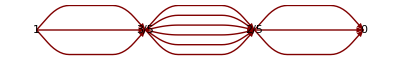

```mathematica
GraphPlot[{1->3/5,1->3/5,1->3/5,3/5->2/5,3/5->2/5,3/5->2/5,3/5->2/5,3/5->2/5,3/5->2/5,2/5->0,2/5->0,2/5->0},DirectedEdges->True, VertexLabeling->True,AspectRatio->.15]
```

Our very small Monte Carlo sample has produced a very rough (!) approximation to the anticipated

```mathematica
Subscript[P, 2]=Subscript[V, 2]=3/5//N
```

0.6

We make the trivial adjustments required to produce a much larger population of such walks

```mathematica
Table[{Subscript[Walk, n]=NestWhileList[RandomChoice[Sum[#⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4],Subscript[σ, 5],Subscript[σ, 6],Subscript[σ, 7],Subscript[σ, 8]},1]⟦1⟧&,Subscript[σ, 2],#≠{1,0,0,0,0,0,0,0}&]},{n,1,1000}];
```

```mathematica
Table[Which[Sum[Subscript[Walk, j]⟦k⟧⟦8⟧,{k,1,Length[Subscript[Walk, j]]}]==0,A,Sum[Subscript[Walk, j]⟦k⟧⟦8⟧,{k,1,Length[Subscript[Walk, j]]}]!=0,B],{j,1,1000}];
```

```mathematica
Tally[%]
```

{{A,597},{B,403}}

and get a much improved approximation to the exact result:

```mathematica
Subscript[P, 2]=Subscript[V, 2]=597/(597+403)//N
```

0.597

Similarly,

```mathematica
Table[{Subscript[Walk, n]=NestWhileList[RandomChoice[Sum[#⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4],Subscript[σ, 5],Subscript[σ, 6],Subscript[σ, 7],Subscript[σ, 8]},1]⟦1⟧&,Subscript[σ, 3],#≠{1,0,0,0,0,0,0,0}&]},{n,1,1000}];
Table[Which[Sum[Subscript[Walk, j]⟦k⟧⟦8⟧,{k,1,Length[Subscript[Walk, j]]}]==0,A,Sum[Subscript[Walk, j]⟦k⟧⟦8⟧,{k,1,Length[Subscript[Walk, j]]}]!=0,B],{j,1,1000}];
Tally[%]
```

{{A,409},{B,591}}

(note how slight was the adjustment required to adjust the initial node) supplies

```mathematica
Subscript[P, 3]=Subscript[V, 3]=409/(409+591)//N
```

0.409

which is a similarly close approximation to the variationally exact result

```mathematica
Subscript[P, 2]=Subscript[V, 2]=2/5//N
```

0.4

Here I show in red the command points where adjustments are to be made if one wants to relocate the input node A, the output node B and/or the node C at which one wants to determine the nodal potential:

Table[{Walk_n=NestWhileList[RandomChoice[Sum[#⟦k⟧T_k,{k,1,8}]→{σ_1,σ_2,σ_3,σ_4,σ_5,σ_6,σ_7,σ_8},1]⟦1⟧&,C,#≠A&]},{n,1,1000}];
Table[Which[Sum[Walk_j⟦k⟧⟦B⟧,{k,1,Length[Walk_j]}]==0,A,Sum[Walk_j⟦k⟧⟦B⟧,{k,1,Length[Walk_j]}]!=0,B],{j,1,1000}];
Tally[%]

### Random walks on DC circuit graphs, revisited

Construct a random symmetric matrix

```mathematica
Table[Subscript[row, k]=Table[RandomInteger[{1,9}],{j,1,8}],{k,1,8}];

RandomSym=%+Transpose[%];

RandomSym//MatrixForm
```

(12 | 13 | 12 | 6 | 14 | 10 | 8 | 12
13 | 6 | 16 | 11 | 15 | 13 | 15 | 10
12 | 16 | 16 | 11 | 9 | 9 | 11 | 15
6 | 11 | 11 | 8 | 14 | 10 | 3 | 9
14 | 15 | 9 | 14 | 14 | 12 | 12 | 10
10 | 13 | 9 | 10 | 12 | 14 | 17 | 12
8 | 15 | 11 | 3 | 12 | 17 | 8 | 13
12 | 10 | 15 | 9 | 10 | 12 | 13 | 10)

```mathematica
Table[RandomSym⟦k⟧/Total[RandomSym⟦k⟧],{k,1,8}]
```

{{4/29,13/87,4/29,2/29,14/87,10/87,8/87,4/29},{13/99,2/33,16/99,1/9,5/33,13/99,5/33,10/99},{4/33,16/99,16/99,1/9,1/11,1/11,1/9,5/33},{1/12,11/72,11/72,1/9,7/36,5/36,1/24,1/8},{7/50,3/20,9/100,7/50,7/50,3/25,3/25,1/10},{10/97,13/97,9/97,10/97,12/97,14/97,17/97,12/97},{8/87,5/29,11/87,1/29,4/29,17/87,8/87,13/87},{12/91,10/91,15/91,9/91,10/91,12/91,1/7,10/91}}

```mathematica
Random𝕋=Transpose[%]

Random𝕋//MatrixForm
```

{{4/29,13/99,4/33,1/12,7/50,10/97,8/87,12/91},{13/87,2/33,16/99,11/72,3/20,13/97,5/29,10/91},{4/29,16/99,16/99,11/72,9/100,9/97,11/87,15/91},{2/29,1/9,1/9,1/9,7/50,10/97,1/29,9/91},{14/87,5/33,1/11,7/36,7/50,12/97,4/29,10/91},{10/87,13/99,1/11,5/36,3/25,14/97,17/87,12/91},{8/87,5/33,1/9,1/24,3/25,17/97,8/87,1/7},{4/29,10/99,5/33,1/8,1/10,12/97,13/87,10/91}}

(4/29 | 13/99 | 4/33 | 1/12 | 7/50 | 10/97 | 8/87 | 12/91
13/87 | 2/33 | 16/99 | 11/72 | 3/20 | 13/97 | 5/29 | 10/91
4/29 | 16/99 | 16/99 | 11/72 | 9/100 | 9/97 | 11/87 | 15/91
2/29 | 1/9 | 1/9 | 1/9 | 7/50 | 10/97 | 1/29 | 9/91
14/87 | 5/33 | 1/11 | 7/36 | 7/50 | 12/97 | 4/29 | 10/91
10/87 | 13/99 | 1/11 | 5/36 | 3/25 | 14/97 | 17/87 | 12/91
8/87 | 5/33 | 1/9 | 1/24 | 3/25 | 17/97 | 8/87 | 1/7
4/29 | 10/99 | 5/33 | 1/8 | 1/10 | 12/97 | 13/87 | 10/91)

```mathematica
Table[Total[Transpose[Random𝕋]⟦1⟧],{k,1,8}]
```

{1,1,1,1,1,1,1,1}

```mathematica
Eigenvalues[Random𝕋]//N
```

{1.,-0.148044,0.105055,-0.0969427,0.0900735,0.0497523,-0.0332477,-0.00920784}

```mathematica
Table[Subscript[srow, k]=Table[(1-KroneckerDelta[j,k])RandomInteger[{1,9}],{j,1,8}],{k,1,8}];

SpinelessRandomSym=%+Transpose[%];

SpinelessRandomSym//MatrixForm
```

(0 | 10 | 12 | 8 | 11 | 8 | 7 | 12
10 | 0 | 10 | 10 | 12 | 13 | 10 | 10
12 | 10 | 0 | 13 | 8 | 9 | 12 | 11
8 | 10 | 13 | 0 | 6 | 12 | 9 | 10
11 | 12 | 8 | 6 | 0 | 11 | 8 | 14
8 | 13 | 9 | 12 | 11 | 0 | 11 | 3
7 | 10 | 12 | 9 | 8 | 11 | 0 | 11
12 | 10 | 11 | 10 | 14 | 3 | 11 | 0)

```mathematica
Table[SpinelessRandomSym⟦k⟧/Total[SpinelessRandomSym⟦k⟧],{k,1,8}];
```

```mathematica
Spineless𝕋=Transpose[%];
```

```mathematica
Spineless𝕋//MatrixForm
```

(0 | 2/15 | 4/25 | 2/17 | 11/70 | 8/67 | 7/68 | 12/71
5/34 | 0 | 2/15 | 5/34 | 6/35 | 13/67 | 5/34 | 10/71
3/17 | 2/15 | 0 | 13/68 | 4/35 | 9/67 | 3/17 | 11/71
2/17 | 2/15 | 13/75 | 0 | 3/35 | 12/67 | 9/68 | 10/71
11/68 | 4/25 | 8/75 | 3/34 | 0 | 11/67 | 2/17 | 14/71
2/17 | 13/75 | 3/25 | 3/17 | 11/70 | 0 | 11/68 | 3/71
7/68 | 2/15 | 4/25 | 9/68 | 4/35 | 11/67 | 0 | 11/71
3/17 | 2/15 | 11/75 | 5/34 | 1/5 | 3/67 | 11/68 | 0)

```mathematica
Table[Total[Transpose[Spineless𝕋]⟦1⟧],{k,1,8}]
```

{1,1,1,1,1,1,1,1}

```mathematica
Eigenvalues[Spineless𝕋]//N
```

{1.,-0.293132,-0.208709,-0.178393,-0.154486,-0.114532,-0.0501955,-0.000552389}

(0 | 1 | 1 | 1 | 0 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 1 | 1 | 1 | 0)

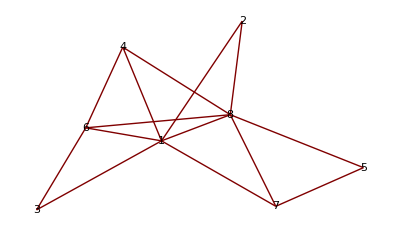

```mathematica
RandomInteger[{},{8,8}];
AdjacencyRandom=Mod[%+Transpose[%],2];
AdjacencyRandom//MatrixForm
GraphPlot[AdjacencyRandom,VertexLabeling->True]
```

```mathematica
Eigenvalues[AdjacencyRandom]//N
```

{4.00269,-2.16805,-1.82878,1.34214,-1.27536,-0.596048,0.343739,0.17967}

```mathematica
AdjacencyRandom
```

{{0,1,1,1,0,1,1,1},{1,0,0,0,0,0,0,1},{1,0,0,0,0,1,0,0},{1,0,0,0,0,1,0,1},{0,0,0,0,0,0,1,1},{1,0,1,1,0,0,0,1},{1,0,0,0,1,0,0,1},{1,1,0,1,1,1,1,0}}

```mathematica
AdjacencyRandom𝕋=Transpose[Table[AdjacencyRandom⟦k⟧/Total[AdjacencyRandom⟦k⟧],{k,1,8}]]
```

{{0,1/2,1/2,1/3,0,1/4,1/3,1/6},{1/6,0,0,0,0,0,0,1/6},{1/6,0,0,0,0,1/4,0,0},{1/6,0,0,0,0,1/4,0,1/6},{0,0,0,0,0,0,1/3,1/6},{1/6,0,1/2,1/3,0,0,0,1/6},{1/6,0,0,0,1/2,0,0,1/6},{1/6,1/2,0,1/3,1/2,1/4,1/3,0}}

```mathematica
%//MatrixForm
```

(0 | 1/2 | 1/2 | 1/3 | 0 | 1/4 | 1/3 | 1/6
1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6
1/6 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0
1/6 | 0 | 0 | 0 | 0 | 1/4 | 0 | 1/6
0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 1/6
1/6 | 0 | 1/2 | 1/3 | 0 | 0 | 0 | 1/6
1/6 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/6
1/6 | 1/2 | 0 | 1/3 | 1/2 | 1/4 | 1/3 | 0)

```mathematica
Eigenvalues[AdjacencyRandom𝕋]//N
```

{1.,-0.596647,-0.5,0.485268,-0.433388,-0.166667,0.149902,0.061532}

#### Close relatives of the resistance matrix

The resistance matrix is (like the Lagrangian and Hamiltonian in mechanics) a "system characterizer," but is made analytically awkward by the presence of the open circuit symbols. Of more immediate relevance to execution of the variational method is the matrix

```mathematica
Subscript[𝔸, cube]=Subscript[ℝ, cube]/.∞->0;
Subscript[𝔸, cube]//MatrixForm
```

(0 | 6 | 0 | 5 | 0 | 4 | 0 | 0
6 | 0 | 4 | 0 | 4 | 0 | 0 | 0
0 | 4 | 0 | 7 | 0 | 0 | 0 | 5
5 | 0 | 7 | 0 | 0 | 0 | 3 | 0
0 | 4 | 0 | 0 | 0 | 9 | 0 | 6
4 | 0 | 0 | 0 | 9 | 0 | 2 | 0
0 | 0 | 0 | 3 | 0 | 2 | 0 | 5
0 | 0 | 5 | 0 | 6 | 0 | 5 | 0)

which is a resistance-weighted version of the "adjacency matrix" that describes the internodal connections present within the cubic array (placement of the graph's "edges"):

```mathematica
Subscript[Adjacency, cube]=({{0, 1, 0, 1, 0, 1, 0, 0}, {1, 0, 1, 0, 1, 0, 0, 0}, {0, 1, 0, 1, 0, 0, 0, 1}, {1, 0, 1, 0, 0, 0, 1, 0}, {0, 1, 0, 0, 0, 1, 0, 1}, {1, 0, 0, 0, 1, 0, 1, 0}, {0, 0, 0, 1, 0, 1, 0, 1}, {0, 0, 1, 0, 1, 0, 1, 0}});
```

On the other hand, of more immediate relevance to execution of the Monte Carlo method is (as will emerge) the "conductance matrix"

```mathematica
Subscript[ℂ, cube]=Subscript[ℝ, cube]^-1;
Subscript[ℂ, cube]//MatrixForm
```

(0 | 1/6 | 0 | 1/5 | 0 | 1/4 | 0 | 0
1/6 | 0 | 1/4 | 0 | 1/4 | 0 | 0 | 0
0 | 1/4 | 0 | 1/7 | 0 | 0 | 0 | 1/5
1/5 | 0 | 1/7 | 0 | 0 | 0 | 1/3 | 0
0 | 1/4 | 0 | 0 | 0 | 1/9 | 0 | 1/6
1/4 | 0 | 0 | 0 | 1/9 | 0 | 1/2 | 0
0 | 0 | 0 | 1/3 | 0 | 1/2 | 0 | 1/5
0 | 0 | 1/5 | 0 | 1/6 | 0 | 1/5 | 0)

—the "matrix of reciprocals,"  which must not be confused either with the "reciprocal of the matrix" (which is undefined) of with the inverse of the weighted adjacency matrix

```mathematica
Inverse[Subscript[𝔸, cube]]//MatrixForm
```

(0 | -24/223 | 0 | 43/223 | 0 | 38/223 | 0 | -41/223
-24/223 | 0 | 237/892 | 0 | 65/446 | 0 | -393/892 | 0
0 | 237/892 | 0 | -59/446 | 0 | -52/223 | 0 | 77/446
43/223 | 0 | -59/446 | 0 | -35/223 | 0 | 143/446 | 0
0 | 65/446 | 0 | -35/223 | 0 | -5/223 | 0 | 23/223
38/223 | 0 | -52/223 | 0 | -5/223 | 0 | 58/223 | 0
0 | -393/892 | 0 | 143/446 | 0 | 58/223 | 0 | -43/446
-41/223 | 0 | 77/446 | 0 | 23/223 | 0 | -43/446 | 0)

### Variational approach to the solution of DC circuit problems: the cubic array

It has always seemed to me to be self-evident that current passing through a resistive DC network will be so partitioned as to minimize the dissipation rate. I have never attempted to construct a formal proof of that proposition (though have frequently asked students to demonstrate its validity in the case of two resistors in parallel). It is a proposition which I have assumed to be well known to electrical engineers, and am surprised to discover that as recently as 1999 it was presented in the pages of the American Journal of Physics (D. A. Van Baak, "Variational alternatives to Kirchhoff's loop theorem in dc circuits," AJP 67, 36 (1999)) as something of a novelty. Van Bank does provide, in his Section III, an elaborate "Proof of the Variational Principle," and traces its ancestory all the way back to Maxwell, who in A Treatise on Electricity & Magnetism §§ 283-284 proves that

"In any system of conductors in which there are no internal electromotive forces the heat generated by currents distributed in    accordance with Ohm's Law is less than if the currents had been distributed in any other manner  consistent with the actual conditions of supply and outflow of the current."

Van Baak also cites a comment added by J. J. Thomson as a footnote to Maxwell's §283; §358 in the 5^thedition of J. Jeans'  The Mathematical Theory of Electricity & Magnetism; the Note which Feynman appended to Chapter 19, "The Principle of Least Action" (Vol. 2 of The Feynman Lectures on Physics), in which Feynman expresses deep interest in the matter and in its unresolved quantum mechanical underpinnings.
 
Here I am content to accept the validity of that variational principle as a given.

We have

```mathematica
DissipationRate=∑_(all branches) Subscript[R, branch] Subscript[J^2, branch]
```

which we must minimize subject to the J_branch-contraints imposed by Kirchhoff's node rule.  

We note in passing that the dissipation function is insensitive to the signs of the branch currents (therefore invariably positive), though the nodal constraints are sign-sensitive. 

It is to illustrate the application of a general variational principle that we look specifically to the case of a cubic array, and it is to verify that the method works that we look first (because in that case we possess a trivially exact solution) to…

#### Dissipation rate & effective resistance of cubic array when all resistors have unit resistance

By assumption

R_(1,2)=R_(1,4)=R_(1,6)=R_(2,1)=R_(2,3)=R_(2,5)=R_(3,2)=R_(3,4)=R_(3,8)=R_(4,1)=R_(4,3)=R_(4,7)=
R_(5,2)=R_(5,6)=R_(5,8)=R_(6,1)=R_(6,5)=R_(6,7)=R_(7,4)=R_(7,6)=R_(7,8)=R_(8,3)=R_(8,5)=R_(8,7)=1;

and  therefore

DissipationRate=1/2((J_(1,2))^2+(J_(1,4))^2+(J_(1,6))^2+(J_(2,1))^2+(J_(2,3))^2+(J_(2,5))^2+(J_(3,2))^2+(J_(3,4))^2+(J_(3,8))^2+(J_(4,1))^2+(J_(4,3))^2+(J_(4,7))^2+
(J_(5,2))^2+(J_(5,6))^2+(J_(5,8))^2+(J_(6,1))^2+(J_(6,5))^2+(J_(6,7))^2+(J_(7,4))^2+(J_(7,6))^2+(J_(7,8))^2+(J_(8,3))^2+(J_(8,5))^2+(J_(8,7))^2)

We could, if we wished, use the antisymmetry of the 𝕁-matrix to reduce the number of terms by a factor of 2 (from 24 to 12), writing

```mathematica
DissipationRate=(Subscript[J, 1,2]^2+Subscript[J, 1,4]^2+Subscript[J, 1,6]^2+Subscript[J, 2,3]^2+Subscript[J, 2,5]^2+Subscript[J, 3,4]^2+Subscript[J, 3,8]^2+Subscript[J, 4,7]^2
+Subscript[J, 5,6]^2+Subscript[J, 5,8]^2+Subscript[J, 6,7]^2+Subscript[J, 7,8]^2)
```

J_(1,2)^2+J_(1,4)^2+J_(1,6)^2+J_(2,3)^2+J_(2,5)^2+J_(3,4)^2+J_(3,8)^2+J_(4,7)^2+J_(5,6)^2+J_(5,8)^2+J_(6,7)^2+J_(7,8)^2

in which we have (arbitrarily) adopted the index-ordering convention

first index < second index

We are looking, therefore, for the point on (in this instance) a 12-dimensional hypersphere which conforms to a set of 8 nodal contraints.

COMPUTATIONAL REMARK: It is always advisable to use only independent variables (taken here to be the currents that lie above the principal diagonal of 𝕁) when assigning work to Mathematica.

#### The nodal constraint relations

In an effort to keep simple things simple, I on this first pass read the nodal constraint relations directly from the adjacency matrix:

(0 | 1 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0)

```mathematica
Subscript[J, 1,2]+Subscript[J, 1,4]+Subscript[J, 1,6]+1==0
Subscript[J, 2,1]+Subscript[J, 2,3]+Subscript[J, 2,5]==0
Subscript[J, 3,2]+Subscript[J, 3,4]+Subscript[J, 3,8]==0
Subscript[J, 4,1]+Subscript[J, 4,3]+Subscript[J, 4,7]==0
Subscript[J, 5,2]+Subscript[J, 5,6]+Subscript[J, 5,8]==0
Subscript[J, 6,1]+Subscript[J, 6,5]+Subscript[J, 6,7]==0
Subscript[J, 7,4]+Subscript[J, 7,6]+Subscript[J, 7,8]==0
Subscript[J, 8,3]+Subscript[J, 8,5]+Subscript[J, 8,7]-1==0
```

If we elect to impose the index-ordering convention those statements become

```mathematica
Constraints={Subscript[J, 1,2]+Subscript[J, 1,4]+Subscript[J, 1,6]+1== 0,
-Subscript[J, 1,2]+Subscript[J, 2,3]+Subscript[J, 2,5]== 0,
-Subscript[J, 2,3]+Subscript[J, 3,4]+Subscript[J, 3,8] == 0,
-Subscript[J, 1,4]-Subscript[J, 3,4]+Subscript[J, 4,7]== 0,
-Subscript[J, 2,5]+Subscript[J, 5,6]+Subscript[J, 5,8]== 0,
-Subscript[J, 1,6]-Subscript[J, 5,6]+Subscript[J, 6,7]== 0,
-Subscript[J, 4,7]-Subscript[J, 6,7]+Subscript[J, 7,8]== 0,
-Subscript[J, 3,8]-Subscript[J, 5,8]-Subscript[J, 7,8]-1== 0}
```

{1+J_(1,2)+J_(1,4)+J_(1,6)==0,-J_(1,2)+J_(2,3)+J_(2,5)==0,-J_(2,3)+J_(3,4)+J_(3,8)==0,-J_(1,4)-J_(3,4)+J_(4,7)==0,-J_(2,5)+J_(5,6)+J_(5,8)==0,-J_(1,6)-J_(5,6)+J_(6,7)==0,-J_(4,7)-J_(6,7)+J_(7,8)==0,-1-J_(3,8)-J_(5,8)-J_(7,8)==0}

Mathematica responds promptly to the following command

```mathematica
Minimize[{DissipationRate,Constraints},{Subscript[J, 1,2],Subscript[J, 1,4],Subscript[J, 1,6] ,Subscript[J, 2,3],Subscript[J, 2,5],Subscript[J, 3,4],Subscript[J, 3,8],Subscript[J, 4,7],Subscript[J, 5,6],Subscript[J, 5,8],Subscript[J, 6,7],Subscript[J, 7,8]}]
```

{5/6,{J_(1,2)→-1/3,J_(1,4)→-1/3,J_(1,6)→-1/3,J_(2,3)→-1/6,J_(2,5)→-1/6,J_(3,4)→1/6,J_(3,8)→-1/3,J_(4,7)→-1/6,J_(5,6)→1/6,J_(5,8)→-1/3,J_(6,7)→-1/6,J_(7,8)→-1/3}}

with results that (by the antisymmetry of the current matrix) can be written

J_(2,1)=J_(4,1)=J_(6,1)=1/3
J_(3,2)=J_(5,2)=J_(3,4)=J_(7,4)=J_(5,6)=J_(7,6)=1/6
J_(8,3)=J_(8,5)=J_(8,7)=1/3

—in precise agreement with the results obtained by the elementary symmetry-based argument developed earlier.

Moreover, we have

```mathematica
Subscript[DissipationRate, minimum]=Subscript[R, effective] Subscript[J, total]^2
```

which, since we have for computational purposes set J_total=1, supplies

R_effective=5/6

—again in precise agreement with a result of the symmetry-based argument.

COMPUTATIONAL REMARK: If we had elected to work with all the elements of 𝕁 we would have had to add to the list of constraints 28 statements of the form J_(m,n)+J_(n,m)==0. Mathematica would than have attempted to provide all possible (but equivalent) formulations of its solution, which would have expanded its output by a factor of 2^28=268435456!

#### Effect of changing the node from which current is extracted

Suppose current is extracted (not, as formerly, from node #8 but) from (say) node #7:

-Graphics-

The symmetry argument now fails, but the variational method very easily accommodates the adjustment. The constraint relations become

```mathematica
NewConstraints={Subscript[J, 1,2]+Subscript[J, 1,4]+Subscript[J, 1,6]+1== 0,
-Subscript[J, 1,2]+Subscript[J, 2,3]+Subscript[J, 2,5]== 0,
-Subscript[J, 2,3]+Subscript[J, 3,4]+Subscript[J, 3,8] == 0,
-Subscript[J, 1,4]-Subscript[J, 3,4]+Subscript[J, 4,7]== 0,
-Subscript[J, 2,5]+Subscript[J, 5,6]+Subscript[J, 5,8]== 0,
-Subscript[J, 1,6]-Subscript[J, 5,6]+Subscript[J, 6,7]== 0,
-Subscript[J, 4,7]-Subscript[J, 6,7]+Subscript[J, 7,8]-1== 0,
-Subscript[J, 3,8]-Subscript[J, 5,8]-Subscript[J, 7,8]== 0};
```

and we obtain

```mathematica
Minimize[{DissipationRate,NewConstraints},{Subscript[J, 1,2],Subscript[J, 1,4],Subscript[J, 1,6] ,Subscript[J, 2,3],Subscript[J, 2,5],Subscript[J, 3,4],Subscript[J, 3,8],Subscript[J, 4,7],Subscript[J, 5,6],Subscript[J, 5,8],Subscript[J, 6,7],Subscript[J, 7,8]}]
```

{3/4,{J_(1,2)→-1/4,J_(1,4)→-3/8,J_(1,6)→-3/8,J_(2,3)→-1/8,J_(2,5)→-1/8,J_(3,4)→0,J_(3,8)→-1/8,J_(4,7)→-3/8,J_(5,6)→0,J_(5,8)→-1/8,J_(6,7)→-3/8,J_(7,8)→1/4}}

The effective resistance has decreased (not surprisingly, since the in/out nodes are now closer together)

R_effective=3/4<5/6

and the currents provide (in their pattern of equalities) a kind of crookedly non-obvious reference to the system's (now broken) symmetry:

J_(4,3)=J_(6,5)=0
J_(3,2)=J_(5,2)=J_(8,3)=J_(8,5)=1/8
J_(2,1)=J_(7,8)=1/4
J_(4,1)=J_(6,1)=J_(7,4)=J_(7,6)=3/8

By symnmetry, only one case remains: extraction from (say) node #6:

-Graphics-

NOTE that the arrows linking nodes #5, 6, 7 & 8 now run counter to our intuitive expectations. We then have

```mathematica
NewNewConstraints={Subscript[J, 1,2]+Subscript[J, 1,4]+Subscript[J, 1,6]+1== 0,
-Subscript[J, 1,2]+Subscript[J, 2,3]+Subscript[J, 2,5]== 0,
-Subscript[J, 2,3]+Subscript[J, 3,4]+Subscript[J, 3,8] == 0,
-Subscript[J, 1,4]-Subscript[J, 3,4]+Subscript[J, 4,7]== 0,
-Subscript[J, 2,5]+Subscript[J, 5,6]+Subscript[J, 5,8]== 0,
-Subscript[J, 1,6]-Subscript[J, 5,6]+Subscript[J, 6,7]-1== 0,
-Subscript[J, 4,7]-Subscript[J, 6,7]+Subscript[J, 7,8]== 0,
-Subscript[J, 3,8]-Subscript[J, 5,8]-Subscript[J, 7,8]== 0};
```

giving

```mathematica
Minimize[{DissipationRate,NewNewConstraints},{Subscript[J, 1,2],Subscript[J, 1,4],Subscript[J, 1,6] ,Subscript[J, 2,3],Subscript[J, 2,5],Subscript[J, 3,4],Subscript[J, 3,8],Subscript[J, 4,7],Subscript[J, 5,6],Subscript[J, 5,8],Subscript[J, 6,7],Subscript[J, 7,8]}]
```

{7/12,{J_(1,2)→-5/24,J_(1,4)→-5/24,J_(1,6)→-7/12,J_(2,3)→-1/24,J_(2,5)→-1/6,J_(3,4)→1/24,J_(3,8)→-1/12,J_(4,7)→-1/6,J_(5,6)→-5/24,J_(5,8)→1/24,J_(6,7)→5/24,J_(7,8)→1/24}}

The effective resistance has been still further reduced:

R_effective=7/12<3/4<5/6

#### Effective resistance and branch currents in cubic array with arbitrary resistors

We wish to associate resistance values R_(m,n) with each of the twelve 1s that appear above the principle diagonal in the adjacency matrix

```mathematica
Subscript[Adjacency, cube]//MatrixForm
```

(0 | 1 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0)

Taking those resistance values to be random real numbers drawn from the unit interval, we have simply to command

```mathematica
Table[Subscript[R, j,k]=AdjacencyCube⟦j⟧⟦k⟧RandomReal[],{j,1,8},{k,j,8}]
```

{{0,0.340908,0,0.198485,0,0.0830912,0,0},{0,0.450098,0,0.120116,0,0,0},{0,0.775587,0,0,0,0.947201},{0,0,0,0.942354,0},{0,0.876514,0,0.678551},{0,0.573901,0},{0,0.195131},{0}}

It is, however, easier on the eye to assume (as do the authors of textbooks) that the resistance values are random integers. Assuming those integers to range between 1 and 99, we command

```mathematica
Table[Subscript[R, j,k]=AdjacencyCube⟦j⟧⟦k⟧RandomInteger[{1,99}],{j,1,8},{k,j,8}]
```

{{0,65,0,99,0,79,0,0},{0,11,0,88,0,0,0},{0,85,0,0,0,7},{0,0,0,69,0},{0,68,0,41},{0,18,0},{0,23},{0}}

The dissipation function now reads

```mathematica
DissipationRandomCube=Sum[Subscript[R, j,k] Subscript[J, j,k]^2,{j,1,8},{k,j,8}]
```

65 J_(1,2)^2+99 J_(1,4)^2+79 J_(1,6)^2+11 J_(2,3)^2+88 J_(2,5)^2+85 J_(3,4)^2+7 J_(3,8)^2+69 J_(4,7)^2+68 J_(5,6)^2+41 J_(5,8)^2+18 J_(6,7)^2+23 J_(7,8)^2

Restoring the input and output nodes to their original (maximally symmetric) placement

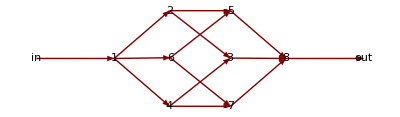

the nodal constraint relations (which are insensitive to resistance assignments, depend only upon connectivity properties of the circuit) retain their original form

```mathematica
Constraints
```

{1+J_(1,2)+J_(1,4)+J_(1,6)==0,-J_(1,2)+J_(2,3)+J_(2,5)==0,-J_(2,3)+J_(3,4)+J_(3,8)==0,-J_(1,4)-J_(3,4)+J_(4,7)==0,-J_(2,5)+J_(5,6)+J_(5,8)==0,-J_(1,6)-J_(5,6)+J_(6,7)==0,-J_(4,7)-J_(6,7)+J_(7,8)==0,-1-J_(3,8)-J_(5,8)-J_(7,8)==0}

So we have

```mathematica
Minimize[{DissipationRandomCube,Constraints},{Subscript[J, 1,2],Subscript[J, 1,4],Subscript[J, 1,6] ,Subscript[J, 2,3],Subscript[J, 2,5],Subscript[J, 3,4],Subscript[J, 3,8],Subscript[J, 4,7],Subscript[J, 5,6],Subscript[J, 5,8],Subscript[J, 6,7],Subscript[J, 7,8]}]
```

{4479379579460/119961617491,{J_(1,2)→-53569681590/119961617491,J_(1,4)→-27517297351/119961617491,J_(1,6)→-38874638550/119961617491,J_(2,3)→-49452430249/119961617491,J_(2,5)→-4117251341/119961617491,J_(3,4)→15315218804/119961617491,J_(3,8)→-64767649053/119961617491,J_(4,7)→-12202078547/119961617491,J_(5,6)→11371337881/119961617491,J_(5,8)→-15488589222/119961617491,J_(6,7)→-27503300669/119961617491,J_(7,8)→-39705379216/119961617491}}

—or more informatively

```mathematica
X=Minimize[{DissipationRandomCube,Constraints},{Subscript[J, 1,2],Subscript[J, 1,4],Subscript[J, 1,6] ,Subscript[J, 2,3],Subscript[J, 2,5],Subscript[J, 3,4],Subscript[J, 3,8],Subscript[J, 4,7],Subscript[J, 5,6],Subscript[J, 5,8],Subscript[J, 6,7],Subscript[J, 7,8]}]//N
```

{37.3401,{J_(1,2)→-0.446557,J_(1,4)→-0.229384,J_(1,6)→-0.324059,J_(2,3)→-0.412235,J_(2,5)→-0.0343214,J_(3,4)→0.127668,J_(3,8)→-0.539903,J_(4,7)→-0.101717,J_(5,6)→0.0947915,J_(5,8)→-0.129113,J_(6,7)→-0.229268,J_(7,8)→-0.330984}}

—from which R_effective and the magnitude/direction of each of the 12 branch currents can be read off.

```mathematica
X⟦2⟧
```

{J_(1,2)→-0.446557,J_(1,4)→-0.229384,J_(1,6)→-0.324059,J_(2,3)→-0.412235,J_(2,5)→-0.0343214,J_(3,4)→0.127668,J_(3,8)→-0.539903,J_(4,7)→-0.101717,J_(5,6)→0.0947915,J_(5,8)→-0.129113,J_(6,7)→-0.229268,J_(7,8)→-0.330984}

```mathematica
Subscript[R, effective]=X⟦1⟧
```

37.3401

```mathematica
Subscript[J, 1,2]=Replace[Subscript[J, 1,2],X⟦2⟧]
```

-0.446557

### Creation and variational DC analysis of a randomly constructed 8-node circuit

There is, of course, nothing special—so far as concerns the essentials of the variational method—about the cubic array, which is distinguished from other (8-node) arrays only by its particular/defining set of connection relations. Nor, for that matter, are 8-node arrays distinguished from N-node arrays in any fundamental way: for the purposes of this discussion I look to 8-node arrays simply because they lead to expressions that fit comfortably onto the page.

Discussion of general—randomly constructed—arrays becomes worth the effort because it forces the invention of certain general graph-analytic procedures.

REMARK: The following discussion might serve as a point of departure for development of a numerical approach to percolation theory.  Drop increasingly many resistors onto (say) a 100 × 100 array of nodes, and watch the conductance, which will increase from 0 to a maximal value. It is to the statistics of such procedures that percolation theory speaks.

```mathematica
Needs["GraphUtilities`"];
```

```mathematica
Construction of random adjacency matrices
```

Repeating this series of commands will generate a random series of 8 × 8 symmetric adjacency matrices—of which there are a total of

```mathematica
2^((8^2-8)/2)
```

268435456

—and will display the associated labeled graph:

(0 | 1 | 0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 0 | 1 | 1
0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 1 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0 | 0 | 1 | 0)

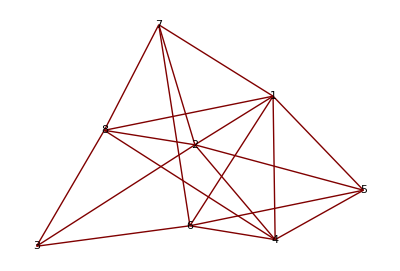

```mathematica
RandomInteger[{},{8,8}];
AdjacencyRandom=Mod[%+Transpose[%],2];
AdjacencyRandom//MatrixForm
GraphPlot[AdjacencyRandom,VertexLabeling->True]
```

Some fraction of those will display one or several disconnected fragments: those are, for most purposes, of little physical interest, and can be discarded.

#### Automated construction of the nodal constraint relations

The following command lists all the edges in the preceding graph

```mathematica
AllEdges=EdgeList[AdjacencyRandom]
```

{{1,2},{1,4},{1,5},{1,6},{1,7},{1,8},{2,1},{2,3},{2,4},{2,5},{2,7},{2,8},{3,2},{3,6},{3,8},{4,1},{4,2},{4,5},{4,6},{4,8},{5,1},{5,2},{5,4},{5,6},{6,1},{6,3},{6,4},{6,5},{6,7},{7,1},{7,2},{7,6},{7,8},{8,1},{8,2},{8,3},{8,4},{8,7}}

of which there are (count 'em) a total of

```mathematica
Length[%]
```

38

if one considers  m⟶n  and  n⟶m  to be distinct. The following commands

```mathematica
Position[AllEdges,1]
Length[%]
```

{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,2},{16,2},{21,2},{25,2},{30,2},{34,2}}

12

inform us that
  • 1 appears as the first element in Parts 1, 2, 3, 4, 5, 6 of AllEdges;
  • 1 appears as the second element in Parts 7, 16, 21, 25, 30, 34 of AllEdges
and that 1 enters into a total of 12 such bilateral pairings: 6 edges have 1 as source point, 6 have 1 as endpoint.

To automate the extraction of that kind of information (which is precisely the information that dictates the formulation of the nodal constraint relations) we introduce definitions

```mathematica
Positions[k_]:=Position[AllEdges,k]
NodeData[j_]:=Table[AllEdges⟦Positions[j]⟦k⟧⟦1⟧⟧,{k,1,Length[Positions[j]]}]
```

From

```mathematica
NodeData[1]
```

{{1,2},{1,4},{1,5},{1,6},{1,7},{1,8},{2,1},{4,1},{5,1},{6,1},{7,1},{8,1}}

we learn that (which is evident already from the graph) node #1 is bilaterally linked to nodes #2, 4, 5, 6 ,7, 8. 

We are now in position to define

```mathematica
IndexOrdering[x_,y_]:=Which[x⩽y,1,x>y,-1]
```

```mathematica
NodalTerms[x_]:=∑_(n=1)^Length[NodeData[x]] IndexOrdering[NodeData[x]⟦n⟧⟦1⟧,NodeData[x]⟦n⟧⟦2⟧] Subscript[J, NodeData[x]⟦n⟧⟦1⟧,NodeData[x]⟦n⟧⟦2⟧]
```

which at node #1 supplies

```mathematica
NodalTerms[1]
```

J_(1,2)+J_(1,4)+J_(1,5)+J_(1,6)+J_(1,7)+J_(1,8)-J_(2,1)-J_(4,1)-J_(5,1)-J_(6,1)-J_(7,1)-J_(8,1)

We list the substitutions that sends sub-diagonal elements of the 𝕁 matrix into the negatives of their super-diagonal counterparts

```mathematica
CurrentAsymmetries=Table[Subscript[J, k,j]->-Subscript[J, j,k],{k,1,8},{j,1,k}]//Flatten
```

{J_(1,1)→-J_(1,1),J_(2,1)→-J_(1,2),J_(2,2)→-J_(2,2),J_(3,1)→-J_(1,3),J_(3,2)→-J_(2,3),J_(3,3)→-J_(3,3),J_(4,1)→-J_(1,4),J_(4,2)→-J_(2,4),J_(4,3)→-J_(3,4),J_(4,4)→-J_(4,4),J_(5,1)→-J_(1,5),J_(5,2)→-J_(2,5),J_(5,3)→-J_(3,5),J_(5,4)→-J_(4,5),J_(5,5)→-J_(5,5),J_(6,1)→-J_(1,6),J_(6,2)→-J_(2,6),J_(6,3)→-J_(3,6),J_(6,4)→-J_(4,6),J_(6,5)→-J_(5,6),J_(6,6)→-J_(6,6),J_(7,1)→-J_(1,7),J_(7,2)→-J_(2,7),J_(7,3)→-J_(3,7),J_(7,4)→-J_(4,7),J_(7,5)→-J_(5,7),J_(7,6)→-J_(6,7),J_(7,7)→-J_(7,7),J_(8,1)→-J_(1,8),J_(8,2)→-J_(2,8),J_(8,3)→-J_(3,8),J_(8,4)→-J_(4,8),J_(8,5)→-J_(5,8),J_(8,6)→-J_(6,8),J_(8,7)→-J_(7,8),J_(8,8)→-J_(8,8)}

and use those substitutions to write the NodalTerms in ways that refer only to the super-diagonal currents (our arbitrarily selected set of independent variables)

```mathematica
IndependentCurrents=Table[Subscript[J, j,k],{j,1,7},{k,j+1,8}]//Flatten
```

{J_(1,2),J_(1,3),J_(1,4),J_(1,5),J_(1,6),J_(1,7),J_(1,8),J_(2,3),J_(2,4),J_(2,5),J_(2,6),J_(2,7),J_(2,8),J_(3,4),J_(3,5),J_(3,6),J_(3,7),J_(3,8),J_(4,5),J_(4,6),J_(4,7),J_(4,8),J_(5,6),J_(5,7),J_(5,8),J_(6,7),J_(6,8),J_(7,8)}

That is accomplished by a command

```mathematica
RefinedNodalTerms[x_]:=Simplify[1/2 NodalTerms[x]/.CurrentAsymmetries]
```

which places us in position finally to tabulate the nodal constraint relations:

```mathematica
NodalConstrints=Table[RefinedNodalTerms[k]==0,{k,1,8}]
```

{J_(1,2)+J_(1,4)+J_(1,5)+J_(1,6)+J_(1,7)+J_(1,8)==0,J_(1,2)+J_(2,3)+J_(2,4)+J_(2,5)+J_(2,7)+J_(2,8)==0,J_(2,3)+J_(3,6)+J_(3,8)==0,J_(1,4)+J_(2,4)+J_(4,5)+J_(4,6)+J_(4,8)==0,J_(1,5)+J_(2,5)+J_(4,5)+J_(5,6)==0,J_(1,6)+J_(3,6)+J_(4,6)+J_(5,6)+J_(6,7)==0,J_(1,7)+J_(2,7)+J_(6,7)+J_(7,8)==0,J_(1,8)+J_(2,8)+J_(3,8)+J_(4,8)+J_(7,8)==0}

These are seen to be 8 in number

```mathematica
Length[%]
```

8

as—one per node—they should be. In use, one has to make trivial by-hand adjustments at the input and output nodes.

#### Completion of the exercise

Specific resistance values (which I will again take to be random integers) are introduced via construction of the dissipation function:

```mathematica
DissipationFunction=Sum[RandomInteger[{1,99}] IndependentCurrents⟦k⟧^2,{k,1,Length[IndependentCurrents]}]
```

95 J_(1,2)^2+62 J_(1,3)^2+4 J_(1,4)^2+86 J_(1,5)^2+77 J_(1,6)^2+29 J_(1,7)^2+59 J_(1,8)^2+50 J_(2,3)^2+14 J_(2,4)^2+65 J_(2,5)^2+70 J_(2,6)^2+75 J_(2,7)^2+71 J_(2,8)^2+69 J_(3,4)^2+57 J_(3,5)^2+48 J_(3,6)^2+73 J_(3,7)^2+61 J_(3,8)^2+34 J_(4,5)^2+10 J_(4,6)^2+38 J_(4,7)^2+22 J_(4,8)^2+40 J_(5,6)^2+42 J_(5,7)^2+71 J_(5,8)^2+54 J_(6,7)^2+60 J_(6,8)^2+61 J_(7,8)^2

The solution of the CD circuit problem lies now immediately at hand: the constraint relations—if we assume current

J=1

to be injected at node #1 and extracted at node #2—become

```mathematica
NodalConstrints
```

```mathematica
{Subscript[J, 1,2]+Subscript[J, 1,4]+Subscript[J, 1,5]+Subscript[J, 1,6]+Subscript[J, 1,7]+Subscript[J, 1,8]+1==0,Subscript[J, 1,2]+Subscript[J, 2,3]+Subscript[J, 2,4]+Subscript[J, 2,5]+Subscript[J, 2,7]+Subscript[J, 2,8]-1==0,Subscript[J, 2,3]+Subscript[J, 3,6]+Subscript[J, 3,8]==0,Subscript[J, 1,4]+Subscript[J, 2,4]+Subscript[J, 4,5]+Subscript[J, 4,6]+Subscript[J, 4,8]==0,Subscript[J, 1,5]+Subscript[J, 2,5]+Subscript[J, 4,5]+Subscript[J, 5,6]==0,Subscript[J, 1,6]+Subscript[J, 3,6]+Subscript[J, 4,6]+Subscript[J, 5,6]+Subscript[J, 6,7]==0,Subscript[J, 1,7]+Subscript[J, 2,7]+Subscript[J, 6,7]+Subscript[J, 7,8]==0,Subscript[J, 1,8]+Subscript[J, 2,8]+Subscript[J, 3,8]+Subscript[J, 4,8]+Subscript[J, 7,8]==0}
```

and so we have

```mathematica
Minimize[DissipationFunction,{Subscript[J, 1,2]+Subscript[J, 1,4]+Subscript[J, 1,5]+Subscript[J, 1,6]+Subscript[J, 1,7]+Subscript[J, 1,8]+1==0,Subscript[J, 1,2]+Subscript[J, 2,3]+Subscript[J, 2,4]+Subscript[J, 2,5]+Subscript[J, 2,7]+Subscript[J, 2,8]-1==0,Subscript[J, 2,3]+Subscript[J, 3,6]+Subscript[J, 3,8]==0,Subscript[J, 1,4]+Subscript[J, 2,4]+Subscript[J, 4,5]+Subscript[J, 4,6]+Subscript[J, 4,8]==0,Subscript[J, 1,5]+Subscript[J, 2,5]+Subscript[J, 4,5]+Subscript[J, 5,6]==0,Subscript[J, 1,6]+Subscript[J, 3,6]+Subscript[J, 4,6]+Subscript[J, 5,6]+Subscript[J, 6,7]==0,Subscript[J, 1,7]+Subscript[J, 2,7]+Subscript[J, 6,7]+Subscript[J, 7,8]==0,Subscript[J, 1,8]+Subscript[J, 2,8]+Subscript[J, 3,8]+Subscript[J, 4,8]+Subscript[J, 7,8]==0},IndependentCurrents]
```

{34000976643669450089350/3060252857340850731589,{J_(1,2)→99347366138057136300/3060252857340850731589,J_(1,3)→0,J_(1,4)→-2225000515331338874620/3060252857340850731589,J_(1,5)→-184885287994158394305/3060252857340850731589,J_(1,6)→-157498681324942381620/3060252857340850731589,J_(1,7)→-358619745893917053350/3060252857340850731589,J_(1,8)→-233595992934551163994/3060252857340850731589,J_(2,3)→290052176478095596716/3060252857340850731589,J_(2,4)→1792926755881721042205/3060252857340850731589,J_(2,5)→278474490402643510448/3060252857340850731589,J_(2,6)→0,J_(2,7)→314680053503278073896/3060252857340850731589,J_(2,8)→284772014937055372024/3060252857340850731589,J_(3,4)→0,J_(3,5)→0,J_(3,6)→-147141446275650239530/3060252857340850731589,J_(3,7)→0,J_(3,8)→-142910730202445357186/3060252857340850731589,J_(4,5)→-6975293184381037290/3060252857340850731589,J_(4,6)→353557633720810325763/3060252857340850731589,J_(4,7)→0,J_(4,8)→85491418913188543942/3060252857340850731589,J_(5,6)→-86613909224104078853/3060252857340850731589,J_(5,7)→0,J_(5,8)→0,J_(6,7)→37696403103886374240/3060252857340850731589,J_(6,8)→0,J_(7,8)→6243289286752605214/3060252857340850731589}}

```mathematica
%//N
```

{11.1105,{J_(1,2)→0.0324638,J_(1,3)→0.,J_(1,4)→-0.727064,J_(1,5)→-0.060415,J_(1,6)→-0.0514659,J_(1,7)→-0.117186,J_(1,8)→-0.0763323,J_(2,3)→0.0947805,J_(2,4)→0.585875,J_(2,5)→0.0909972,J_(2,6)→0.,J_(2,7)→0.102828,J_(2,8)→0.0930551,J_(3,4)→0.,J_(3,5)→0.,J_(3,6)→-0.0480815,J_(3,7)→0.,J_(3,8)→-0.046699,J_(4,5)→-0.00227932,J_(4,6)→0.115532,J_(4,7)→0.,J_(4,8)→0.0279361,J_(5,6)→-0.0283029,J_(5,7)→0.,J_(5,8)→0.,J_(6,7)→0.0123181,J_(6,8)→0.,J_(7,8)→0.00204012}}

```mathematica
%//TableForm
```

11.1105 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
J_(1,2)→0.0324638 | J_(1,3)→0. | J_(1,4)→-0.727064 | J_(1,5)→-0.060415 | J_(1,6)→-0.0514659 | J_(1,7)→-0.117186 | J_(1,8)→-0.0763323 | J_(2,3)→0.0947805 | J_(2,4)→0.585875 | J_(2,5)→0.0909972 | J_(2,6)→0. | J_(2,7)→0.102828 | J_(2,8)→0.0930551 | J_(3,4)→0. | J_(3,5)→0. | J_(3,6)→-0.0480815 | J_(3,7)→0. | J_(3,8)→-0.046699 | J_(4,5)→-0.00227932 | J_(4,6)→0.115532 | J_(4,7)→0. | J_(4,8)→0.0279361 | J_(5,6)→-0.0283029 | J_(5,7)→0. | J_(5,8)→0. | J_(6,7)→0.0123181 | J_(6,8)→0. | J_(7,8)→0.00204012

The statements

```mathematica
Subscript[J, 1,3]=Subscript[J, 2,6]=Subscript[J, 3,4]=Subscript[J, 3,5]=Subscript[J, 3,7]=Subscript[J, 4,7]=Subscript[J, 5,7]=Subscript[J, 5,8]=Subscript[J, 6,8]=0
```

reflect the circumstance—evident in the design of the graph

-Graphics-

—that no wires (edges) connect those nodes. We can assign any values we please to the resistances in those "virtual wires:" such assignments affect the appearance of the dissipation function, but have no effect upon the physics.

### Monte Carlo approach to the solution of DC circuit problems

First some points of terminology: The nodes that are adjacent to node #m (in the sense: connected directly to #m by a wire/edge) will be said to be "neighbors" of #m. The term refers only to immediate neighbors, not to more remote neighbors that can be reached only by passage through one or more intermediate nodes. We will write N[m] to refer collectively to #m's population of neighbors.

Kirchhoff's nodal rule can now be phrased

∑_(n ∈ N[m]) J_(m,n)==0

#### How the potential at node #m relates to the potentials at neighboring nodes

Let the potential at the entry node into a circuit be V, the potential at the exit node (ground) be 0, and the potential at the m^th node (after establishment of the steady DC state) be V_m.  The nodal rule can (given Ohm's Law) be phrased

∑_(n ∈ N[m]) (V_n-V_m)/(R_(m,n))==0

or again

V_m×∑_(n ∈ N[m]) 1/(R_(m,n))=∑_(n ∈ N[m]) V_n/(R_(m,n))

At this point it becomes more convenient/natural to speak of "conductances" than of "resistances." In that language we have

V_m×∑_(n ∈ N[m]) C_(m,n)=∑_(n ∈ N[m]) C_(m,n)V_n

whence

V_m=∑_(n ∈ N[m]) (C_(m,n))/C_m V_n     where     C_m=∑_(k ∈ N[m]) C_(m,k)

We note in this connection that, for any given m, the numbers (C_(m,n))/C_mare—like probabilities!—positive real numbers with the property that they sum to unity:

∑_(n ∈ N[m]) (C_(m,n))/C_m=1

REMARK: The signal virtue of the variational approach to the solution of DE circuit problems is that it proceeds without reference to the nodal potentials (therefore without appeal to Kirchhoff's awkward loop rule). It permits the nodal potential always to be recovered "after the fact." The Monte Carlo approach, on the other hand, assigns primary importance to the nodal potentials, though it exploits only a particular property of the nodal potentials that is rooted in Kirchhoff's node rule, and it too proceeds without appeal to the loop rule.

#### Contact with the theory of random walks on graphs

Let P_m be the probability that a walker, starting at node #m, reaches the exit node without having visited the entry node. Clearly

P_(exit node)=1
P_(entry node)=0

It is clear also that a walker, upon departing from node #m, must after one step visit one or another of the nodes in his immediate neighborhood, N[m]. If his first step takes him to neighboring node #n then his probability of success (i.e., of reaching the exit node  without having visited the entry node) has become P_n. From the statistical independence of the wlker's steps we conclude that

P_m=∑_(n ∈ N[m]) prob[n⟵m]P_n

Suppose we were to postulate (as seems physically plausible if our walker is an electron) that

prob[n⟵m]=conductance[n⟵m]/(∑_(n ∈ N[m]) conductance[n⟵m])=∑_(n ∈ N[m]) (C_(m,n))/C_m

It then follows that

∑_(n ∈ N[m]) prob[n⟵m]=1  : (the walker  cannot linger, but
steps with certainty to one or
 another of the neighboring nodes)

and

P_m=∑_(n ∈ N[m]) (C_(m,n))/C_m P_n

We are brought thus to this remarkable conclusion: If

prob[n⟵m]=∑_(n ∈ N[m]) (C_(m,n))/C_m

then the nodal potentials V_n and the nodal probabilities P_n—because they satisfy the same equation—are equal! The Monte Carlo method estimates the latter to obtain approximate evaluations of the former.

#### From conductance matrix to transition matrix

Suppose we possess only probabilistic information concerning the present location of the walker, and elect to display that information as a "stochastic vector"

(p_1
p_2
p_3
⋮
p_8)_n

One step later the stochastic vector becomes

(p_1
p_2
p_3
⋮
p_8)_(n+1)=(prob[1⟵1] | prob[1⟵2] | prob[1⟵3] | ⋯ | prob[1⟵8]
prob[2⟵1] | prob[2⟵2] | prob[2⟵3] | ⋯ | prob[2⟵8]
prob[3⟵1] | prob[3⟵2] | prob[3⟵3] | ⋯ | prob[3⟵8]
⋮ | ⋮ | ⋮ | ⋱ | ⋮
prob[8⟵1] | prob[8⟵2] | prob[8⟵3] | ⋯ | prob[8⟵8])(p_1
p_2
p_3
⋮
p_8)_n≡𝕋(p_1
p_2
p_3
⋮
p_8)_n

The "transition martrix" ("Markoff matrix") has these distinguishing properties:
  • all elements are interpretable as probabilities (i.e., are non-negative real numbers ⩽ 1);
  • the elements in each column sum to unity (so as to insure that ()_(n+1) is again stochastic).
  
In circuit-theoretic applications the transition matrix

𝕋=(0 | (C_(1,2))/C_2 | (C_(1,3))/C_3 | ⋯ | (C_(1,8))/C_8
(C_(2,1))/C_1 | 0 | (C_(2,3))/C_3 | ⋯ | (C_(2,8))/C_8
(C_(3,1))/C_1 | (C_(3,2))/C_2 | 0 | ⋯ | (C_(3,8))/C_8
⋮ | ⋮ | ⋮ | ⋱ | ⋮
(C_(8,1))/C_1 | (C_(8,2))/C_2 | (C_(8,3))/C_3 | ⋯ | 0)

conveys all possibile information about (1) the values of the restances present in the circuit, and (2) how they are connected (as—in their own ways—do ℝ and ℂ), but supplies no indication of at what nodes the circuit has been connected to an external power source. In the general theory of random walks on graphs, 𝕋 provides a sharp tool for tracing the evolving statistics of infinitely large populations of walks

(p_1
p_2
p_3
⋮
p_8)_1⟶(p_1
p_2
p_3
⋮
p_8)_2⟶(p_1
p_2
p_3
⋮
p_8)_3⟶ ⋯ ⟶(p_1
p_2
p_3
⋮
p_8)_asymptotic

of infinitely large populations of walks—what might be called the "statistical mechanics" of walks. But in the random walk approach to DC circuit theory we are asked to examine large populations of individual random walks

1^st node ⟶ 2^nd node ⟶ 3^rd node ⟶ ⋯

and to record the fraction of those which answer to some specified criterion: in short, to estimate the "probabilty of success". 

The 𝕋 matrix is—by itself—unable to accomplish such an assignment. We are obliged to unpack the information incorporated into the design of 𝕋 and to use it to assemble some new tools. 

To that end, I will work in reference to a complete 8-node graph

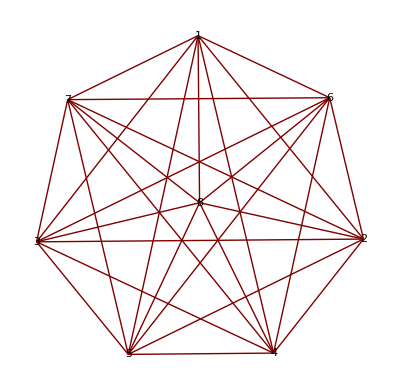

with a rendomly generated "no lingering allowed" 𝕋-matrix.

#### Representation of momentary state

The walker stands at each moment (not probably but) with certainty on one or another of the nodes, represented in the present formalism by one or another of the following specialized stochastic vectors:

```mathematica
Table[Subscript[σ, j]=Transpose[{Table[KroneckerDelta[j,k],{k,1,8}]}],{j,1,8}];
Table[MatrixForm[Subscript[σ, j]],{j,1,8}]
```

{(1
0
0
0
0
0
0
0),(0
1
0
0
0
0
0
0),(0
0
1
0
0
0
0
0),(0
0
0
1
0
0
0
0),(0
0
0
0
1
0
0
0),(0
0
0
0
0
1
0
0),(0
0
0
0
0
0
1
0),(0
0
0
0
0
0
0
1)}

Though column vectors speak most clearly to the habituated eye, they become unwieldy when presented serially on the page, so I will sometimes use simple lists as state-descriptors

```mathematica
Table[Subscript[τ, j]=Table[KroneckerDelta[j,k],{k,1,8}],{j,1,8}];
Table[Subscript[τ, j],{j,1,8}]
```

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

#### Construction of a random "no lingering allowed" 𝕋-matrix

The following sequence of commands does the job:

```mathematica
Table[Subscript[t, j]=Table[(1-KroneckerDelta[j,k])RandomInteger[{1,9}],{k,1,8}],{j,1,8}];

𝕥=Table[Subscript[T, j]=Subscript[t, j]/Total[Subscript[t, j]],{j,1,8}];

𝕋=Transpose[𝕥];
𝕋//MatrixForm
```

(0 | 9/38 | 7/29 | 1/15 | 1/4 | 3/22 | 1/14 | 7/39
3/17 | 0 | 9/29 | 1/6 | 1/12 | 1/11 | 2/7 | 4/39
5/34 | 2/19 | 0 | 7/30 | 5/24 | 2/11 | 5/28 | 2/39
2/17 | 1/19 | 2/29 | 0 | 1/24 | 3/22 | 5/28 | 1/39
9/34 | 7/38 | 1/29 | 1/15 | 0 | 3/11 | 3/28 | 3/13
5/34 | 1/19 | 4/29 | 7/30 | 1/4 | 0 | 1/7 | 7/39
1/17 | 9/38 | 3/29 | 1/5 | 1/24 | 3/22 | 0 | 3/13
3/34 | 5/38 | 3/29 | 1/30 | 1/8 | 1/22 | 1/28 | 0)

The matrix is asymmetric (the principle of detailed balance is inoperative), as the 𝕋-matrices associated with most DC circuits can be expected to be, and even though the ℝ-matrix from which they derive is symmetric. The asymmetry stems—as mentioned previously—from the fact that, though the numerators are symmetric,  different denominators are (typially) encountered in each column. The 0s on the principal diagonal deny to the walker the option of standing in place: he is obliged to keep moving.

#### Method for generating individual random walks

If the walker stands momentarily on node #m (i.e., is in state σ_m) then where he will stand one step later is determined probabilistically by the numbers that appear in the m^th column of 𝕋.  To that ordered list of numbers we already gave a name while constructing 𝕋. In (for example) the 3^rd column we encounter the list

```mathematica
Subscript[T, 3]
```

{7/29,9/29,0,2/29,1/29,4/29,3/29,3/29}

from which we learn that

σ_3⟶(σ_1 with probablility 7/29
σ_2 with probablility 9/29
σ_3 with probablility 0
σ_4 with probablility 2/29
σ_5 with probablility 1/29
σ_6 with probablility 4/29
σ_7 with probablility 3/29
σ_8 with probablility 3/29)

and that the walker goes somewhere (else) with certainty, since

```mathematica
Total[Subscript[T, 3]]
```

1

NOTE: At this point I find it convenient to abandon column vectors σ in favor of simple lists τ as my state identifiers.

The following command asks Mathematica to a select a state from {τ_1,τ_2,τ_3,τ_4,τ_5,τ_6,τ_7,τ_8}, with "which one" determined by the elements of T_3, which acts here like an 8-sided die. Thus

```mathematica
RandomChoice[Subscript[T, 3]->{Subscript[τ, 1],Subscript[τ, 2],Subscript[τ, 3],Subscript[τ, 4],Subscript[τ, 5],Subscript[τ, 6],Subscript[τ, 7],Subscript[τ, 8]},1]⟦1⟧
```

{0,0,0,0,1,0,0,0}

which on repetition yields an assortment of results; here is a list of 10 "first steps away from node #3":

```mathematica
Table[RandomChoice[Subscript[T, 3]->{Subscript[τ, 1],Subscript[τ, 2],Subscript[τ, 3],Subscript[τ, 4],Subscript[τ, 5],Subscript[τ, 6],Subscript[τ, 7],Subscript[τ, 8]},1]⟦1⟧,{k,1,10}]//TableForm
```

0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1

To take a 2^nd step Mathematica must be equipped with means of discovering where its 1^st step has taken it, which it can learn from the placement of the 1 in the new state vector. The following command—asssembled "by hand"—creates a different 5-step walk away from node #3 every time it is repeated:

```mathematica
Subscript[τ, 3]
RandomChoice[Sum[%⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[τ, 1],Subscript[τ, 2],Subscript[τ, 3],Subscript[τ, 4],Subscript[τ, 5],Subscript[τ, 6],Subscript[τ, 7],Subscript[τ, 8]},1]⟦1⟧
RandomChoice[Sum[%⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[τ, 1],Subscript[τ, 2],Subscript[τ, 3],Subscript[τ, 4],Subscript[τ, 5],Subscript[τ, 6],Subscript[τ, 7],Subscript[τ, 8]},1]⟦1⟧
RandomChoice[Sum[%⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[τ, 1],Subscript[τ, 2],Subscript[τ, 3],Subscript[τ, 4],Subscript[τ, 5],Subscript[τ, 6],Subscript[τ, 7],Subscript[τ, 8]},1]⟦1⟧
RandomChoice[Sum[%⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[τ, 1],Subscript[τ, 2],Subscript[τ, 3],Subscript[τ, 4],Subscript[τ, 5],Subscript[τ, 6],Subscript[τ, 7],Subscript[τ, 8]},1]⟦1⟧
RandomChoice[Sum[%⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[τ, 1],Subscript[τ, 2],Subscript[τ, 3],Subscript[τ, 4],Subscript[τ, 5],Subscript[τ, 6],Subscript[τ, 7],Subscript[τ, 8]},1]⟦1⟧
```

{0,0,1,0,0,0,0,0}

{0,0,0,0,0,0,1,0}

{0,1,0,0,0,0,0,0}

{0,0,0,0,0,1,0,0}

{0,0,0,0,1,0,0,0}

{0,1,0,0,0,0,0,0}

If, however, we have interest in long walks then that "by hand" procedure becomes excessively tedious; we need an automated procedure. This works:

```mathematica
NestList[RandomChoice[Sum[#⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[τ, 1],Subscript[τ, 2],Subscript[τ, 3],Subscript[τ, 4],Subscript[τ, 5],Subscript[τ, 6],Subscript[τ, 7],Subscript[τ, 8]},1]⟦1⟧&,Subscript[τ, 3],10]//TableForm
```

0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0

To be in position to examine the statistical properties of populations of walks it is necessary to display each individual walk as a named object—a list of lists (i.e., of successive states). That is easily accomplished: here is a short (5-member) list of short (10-step) walks (each of which departs from node #3):

```mathematica
NestGeneratedList10=Table[NestList[RandomChoice[Sum[#⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[τ, 1],Subscript[τ, 2],Subscript[τ, 3],Subscript[τ, 4],Subscript[τ, 5],Subscript[τ, 6],Subscript[τ, 7],Subscript[τ, 8]},1]⟦1⟧&,Subscript[τ, 3],10],{j,1,5}];
Table[TableForm[NestGeneratedList10⟦k⟧],{k,1,5}]
```

{0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0,0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0,0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1,0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0,0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0}

### Digression: Monte Carlo evidence of equilibration

Suppose a walker begins his walk at (say) node #1. What is the probability that after (say) 15 steps he stands on node #n (n  = 1, 2, … 8)? Iteration of the transition matrix 𝕋 supplies

```mathematica
Table[MatrixForm[N[MatrixPower[𝕋,k].Subscript[σ, 1]]],{k,0,15}]
```

{(1.
0.
0.
0.
0.
0.
0.
0.),(0.
0.176471
0.147059
0.117647
0.264706
0.147059
0.0588235
0.0882353),(0.191404
0.126531
0.142941
0.0632794
0.112193
0.14744
0.131983
0.0842279),(0.141388
0.157786
0.134301
0.0895439
0.156911
0.131309
0.112887
0.0758734),(0.154573
0.146603
0.138909
0.0807483
0.142509
0.137488
0.119442
0.0797289),(0.150852
0.150523
0.137109
0.0835403
0.146788
0.135449
0.117419
0.0783189),(0.151927
0.149222
0.137713
0.0826877
0.145552
0.136039
0.118076
0.0787834),(0.151609
0.149643
0.137526
0.0829455
0.145899
0.135881
0.117859
0.0786368),(0.151704
0.14951
0.137581
0.0828678
0.145803
0.135921
0.117931
0.0786819),(0.151675
0.149552
0.137566
0.0828913
0.145829
0.135911
0.117907
0.0786682),(0.151684
0.149539
0.13757
0.0828842
0.145822
0.135913
0.117915
0.0786723),(0.151682
0.149543
0.137569
0.0828863
0.145824
0.135913
0.117913
0.0786711),(0.151682
0.149541
0.137569
0.0828857
0.145823
0.135913
0.117913
0.0786715),(0.151682
0.149542
0.137569
0.0828859
0.145824
0.135913
0.117913
0.0786714),(0.151682
0.149542
0.137569
0.0828858
0.145823
0.135913
0.117913
0.0786714),(0.151682
0.149542
0.137569
0.0828858
0.145823
0.135913
0.117913
0.0786714)}

from which it becomes evident that the stochastic state vector is converging upon an asymptotically steady state. What we witness here is an "equilibration process."

We draw now upon some general properties of 𝕋-matrices:

1) The leading eigenvalue of a 𝕋 matrix is invariably unity, and the others (whether real or complex) have absolute values that are less than unity:

```mathematica
Abs[N[Eigenvalues[𝕋]]]
```

{1.,0.308961,0.23539,0.23539,0.160659,0.114972,0.114972,0.0806084}

2) The eigenvectors of a 𝕋 matrix are, as supplied to us by Mathematica, normalized. The leading eigenvector is (by the Perron-Frobenius theorem) the only eigenvector with the properties that all of its elements have the same sign (which can be taken  to be positive), and it is, moreover, the only eigenvector with the property that the sum of its elements does not vanish:

```mathematica
Table[Chop[Total[N[Eigenvectors[𝕋]⟦k⟧]]],{k,1,8}]
```

{12.7111,0,0,0,0,0,0,0}

It is, therefore, the only eigenvector that can be "unitized" (meaning "rescaled to that the sum of its elements is unity"). When so unitized it becomes interpretable as a "stochastic vector." In the present instance that vector is

```mathematica
Subscript[v, ∞]=Transpose[{N[Eigenvectors[𝕋]⟦1⟧]/Total[N[Eigenvectors[𝕋]⟦1⟧]]}]//MatrixForm
```

(0.151682
0.149542
0.137569
0.0828858
0.145823
0.135913
0.117913
0.0786714)

3) It follows from (1) and (2) that, for any initial stochastic vector v_0 one has

MatrixPower[𝕋,n].v_0 ⟶ v_∞   as   n ⟶ ∞

—precisely as (just above, where we took v_0=σ_1) we demonstrated by explicit calculation.

So much by way of preparation. The idea now is to construct a very long (10,000-step) walk, and to look to the frequency with which the various nodes are visited :

```mathematica
Walk10000=NestList[RandomChoice[Sum[#⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[τ, 1],Subscript[τ, 2],Subscript[τ, 3],Subscript[τ, 4],Subscript[τ, 5],Subscript[τ, 6],Subscript[τ, 7],Subscript[τ, 8]},1]⟦1⟧&,Subscript[τ, 1],10000];
```

```mathematica
Table[Total[Table[Walk10000⟦j⟧⟦k⟧,{j,1,1000}]],{k,1,8}]/1000//N
```

{0.156,0.147,0.129,0.084,0.146,0.134,0.12,0.084}

Here I compare the results of that "Monte Carlo approximation" with the exact results obtained earlier:

```mathematica
{MatrixForm[Transpose[{%}]],Subscript[v, ∞]}
```

{((0.156)
(0.147)
(0.129)
(0.084)
(0.146)
(0.134)
(0.12)
(0.084)),(0.151682
0.149542
0.137569
0.0828858
0.145823
0.135913
0.117913
0.0786714)}

Accuracy could be improved by taking a longer walk, but we must expect the rate of improvement to be slow, going as roughly

√(number of steps)

### Random walk method applied to solution of cubic DC array problems

Previously we demonstrated the variational method as it applies to a cubic array in which the conductance matrix read

```mathematica
Subscript[ℂ, cube]=({{0, 1/6, 0, 1/5, 0, 1/4, 0, 0}, {1/6, 0, 1/4, 0, 1/4, 0, 0, 0}, {0, 1/4, 0, 1/7, 0, 0, 0, 1/5}, {1/5, 0, 1/7, 0, 0, 0, 1/3, 0}, {0, 1/4, 0, 0, 0, 1/9, 0, 1/6}, {1/4, 0, 0, 0, 1/9, 0, 1/2, 0}, {0, 0, 0, 1/3, 0, 1/2, 0, 1/5}, {0, 0, 1/5, 0, 1/6, 0, 1/5, 0}});
```

```mathematica
Table[Subscript[T, k]=(Subscript[ℂ, cube]⟦k⟧)/Total[Subscript[ℂ, cube]⟦k⟧],{k,1,8}]
```

{{0,10/37,0,12/37,0,15/37,0,0},{1/4,0,3/8,0,3/8,0,0,0},{0,35/83,0,20/83,0,0,0,28/83},{21/71,0,15/71,0,0,0,35/71,0},{0,9/19,0,0,0,4/19,0,6/19},{9/31,0,0,0,4/31,0,18/31,0},{0,0,0,10/31,0,15/31,0,6/31},{0,0,6/17,0,5/17,0,6/17,0}}

```mathematica
Subscript[𝕋, cube]=Transpose[%];
Subscript[𝕋, cube]//MatrixForm
```

(0 | 1/4 | 0 | 21/71 | 0 | 9/31 | 0 | 0
10/37 | 0 | 35/83 | 0 | 9/19 | 0 | 0 | 0
0 | 3/8 | 0 | 15/71 | 0 | 0 | 0 | 6/17
12/37 | 0 | 20/83 | 0 | 0 | 0 | 10/31 | 0
0 | 3/8 | 0 | 0 | 0 | 4/31 | 0 | 5/17
15/37 | 0 | 0 | 0 | 4/19 | 0 | 15/31 | 0
0 | 0 | 0 | 35/71 | 0 | 18/31 | 0 | 6/17
0 | 0 | 28/83 | 0 | 6/19 | 0 | 6/31 | 0)

We will assume as before that current is injected/extracted from the nodes shown in the figure:

We assume the potential at the input node is 0, and at the output node is V = 1 (and so will have to use the known value of R_effective to rescale our results to obtain agreement with our former assumption that the total current was J = 1). We ask for the potential at (say) node #3. To that end, we construct a large population of walks that depart from node #3 and ask for the value of P_3, i.e., for the fraction of them that manage to reach node #1 without having visited node #8. 

To phrase the issue more generally: Given a graph (DC circuit) and an associated (generally unbalanced) transition matrix 𝕋, we seek a numerical estimate of the probability that a walker who starts from C will arrive at A without visiting B.
 
Clearly, that probability is 1 in the case C = A, and 0 in the case C = B. 

For purposes of discussion, I will—as stated above—take

A={0,0,0,0,0,0,1}
B={1,0,0,0,0,0,0}

which leaves our walker with a total of 6 non-trivial points C of departure (nodes #2 through 7).

My plan is to construct a command that generates walks that begin at C and automatically stop at A, then to resolve those walks into two classes : those that DID NOT visit B en route to A, and those that DID visit B.

#### Generating walks that automatically stop upon first arrival at A

We make use of Mathematica's NestWhileList command. The following command generates a list 50-member list of named walks, each of which begins at C = {0, 0, 1, 0, 0, 0, 0, 0} and ends with the first visit to A = {0, 0, 0, 0, 0, 0, 0, 1}:

```mathematica
Table[{Subscript[Walk, n]=NestWhileList[RandomChoice[Sum[#⟦k⟧Subscript[T, k],{k,1,8}]->{Subscript[τ, 1],Subscript[τ, 2],Subscript[τ, 3],Subscript[τ, 4],Subscript[τ, 5],Subscript[τ, 6],Subscript[τ, 7],Subscript[τ, 8]},1]⟦1⟧&,Subscript[τ, 3],#≠{0,0,0,0,0,0,0,1}&]},{n,1,20}];
```

Here are a representative few of those walks :

```mathematica
Table[{j,Subscript[Walk, j]},{j,15,25}]//TableForm
```

15 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
16 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
17 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
18 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
19 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
20 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
21 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
22 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
23 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
24 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
25 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1

We notice that some of those walks visit B = {1, 0, 0, 0, 0, 0, 0, 0} one or more times en route C ⟶ A, while others successfully manage to avoid B.

The idea now is to examine the walks, one at a time, and to print A if the 1s in the initial place sum to 0—signifying that B has been successfully avoided—and in all other cases to print B. Here are iollustrative instances of a command that is seen by inspection to accomplish that objective:

```mathematica
Which[Sum[Subscript[Walk, 24]⟦k⟧⟦1⟧,{k,1,Length[Subscript[Walk, 24]]}]==0,A,Sum[Subscript[Walk, 24]⟦k⟧⟦1⟧,{k,1,Length[Subscript[Walk, 24]]}]!=0, B]
```

A

```mathematica
Which[Sum[Subscript[Walk, 25]⟦k⟧⟦1⟧,{k,1,Length[Subscript[Walk, 25]]}]==0,A,Sum[Subscript[Walk, 25]⟦k⟧⟦1⟧,{k,1,Length[Subscript[Walk, 25]]}]!=0, B]
```

B

Looking to the 50 - member set of walks, we get

```mathematica
Table[Which[Sum[Subscript[Walk, j]⟦k⟧⟦1⟧,{k,1,Length[Subscript[Walk, j]]}]==0,A,Sum[Subscript[Walk, j]⟦k⟧⟦1⟧,{k,1,Length[Subscript[Walk, j]]}]!=0,B],{j,1,50}]
Tally[%]
```

{A,A,A,A,A,A,B,A,A,A,A,A,A,A,A,A,B,B,A,A,B,B,A,A,B,A,B,B,A,A,A,A,A,A,A,A,A,A,A,A,B,B,B,A,A,B,A,A,A,B}

{{A,37},{B,13}}

We conclude on the basis of this small amount of Monte Carlo data that the probability of a successful B-avoiding walk C ⟶ A is

```mathematica
ProbOfSuccess=37/50//N
ProbOfFailure=13/50//N

ProbOfSuccess+ProbOfFailure
```

0.74

0.26

1.

In quest of more accurate estimates we look to a 100,000-member population of such walks

RETURN TO THIS POINT LATER

```mathematica
Eigenvalues[Subscript[𝕋, cube]]//N
```

{-1.,1.,-0.561936,0.561936,-0.245191,0.245191,-0.198417,0.198417}

```mathematica
Eigenvectors[Subscript[𝕋, cube]]⟦1⟧//N
Total[%]
Eigenvectors[Subscript[𝕋, cube]]⟦2⟧//N
Total[%]
```

{-1.08824,1.17647,-1.04622,1.19328,-0.931373,1.51961,-1.82353,1.}

0.

{1.08824,1.17647,1.04622,1.19328,0.931373,1.51961,1.82353,1.}

9.77871

ℝ_unitcube=ℂ_unitcube=(0 | 1 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0)

(which is just the adjacency matrix of the cube) and the associated transition matrix reads

```mathematica
Subscript[𝕋, unitcube]=({{0, 1/3, 0, 1/3, 0, 1/3, 0, 0}, {1/3, 0, 1/3, 0, 1/3, 0, 0, 0}, {0, 1/3, 0, 1/3, 0, 0, 0, 1/3}, {1/3, 0, 1/3, 0, 0, 0, 1/3, 0}, {0, 1/3, 0, 0, 0, 1/3, 0, 1/3}, {1/3, 0, 0, 0, 1/3, 0, 1/3, 0}, {0, 0, 0, 1/3, 0, 1/3, 0, 1/3}, {0, 0, 1/3, 0, 1/3, 0, 1/3, 0}});
```

The symmetry of this matrix is atypical, and indicated that the principle of detailed balance

prob[b⟵a]=prob[a⟵b]    :    all a and b

is operative. But circuit-theoretic transition matrices are typically asymmetric (i.e., refer to "unbalanced walks"), because—though ℂ itself is invariably symmetric—the denominators in the respective columns of 𝕋 are typically unequal.

```mathematica
Eigenvalues[Subscript[𝕋, unitcube]]
```

{-1,1,-1/3,-1/3,-1/3,1/3,1/3,1/3}

```mathematica
Table[Total[Eigenvectors[Subscript[𝕋, unitcube]]⟦k⟧],{k,1,8}]
```

{0,8,0,0,0,0,0,0}

```mathematica
Transpose[{(Eigenvectors[Subscript[𝕋, unitcube]]⟦2⟧)/Total[Eigenvectors[Subscript[𝕋, unitcube]]⟦2⟧]}]//MatrixForm
```

(1/8
1/8
1/8
1/8
1/8
1/8
1/8
1/8)

```mathematica
Transpose[{Eigenvectors[Subscript[𝕋, unitcube]]⟦1⟧}]//MatrixForm
```

(-1
1
-1
1
-1
1
-1
1)

```mathematica
Table[MatrixForm[N[MatrixPower[Subscript[𝕋, unitcube],k].({{1}, {0}, {0}, {0}, {0}, {0}, {0}, {0}})]],{k,0,15}]
```

{(1.
0.
0.
0.
0.
0.
0.
0.),(0.
0.333333
0.
0.333333
0.
0.333333
0.
0.),(0.333333
0.
0.222222
0.
0.222222
0.
0.222222
0.),(0.
0.259259
0.
0.259259
0.
0.259259
0.
0.222222),(0.259259
0.
0.246914
0.
0.246914
0.
0.246914
0.),(0.
0.251029
0.
0.251029
0.
0.251029
0.
0.246914),(0.251029
0.
0.249657
0.
0.249657
0.
0.249657
0.),(0.
0.250114
0.
0.250114
0.
0.250114
0.
0.249657),(0.250114
0.
0.249962
0.
0.249962
0.
0.249962
0.),(0.
0.250013
0.
0.250013
0.
0.250013
0.
0.249962),(0.250013
0.
0.249996
0.
0.249996
0.
0.249996
0.),(0.
0.250001
0.
0.250001
0.
0.250001
0.
0.249996),(0.250001
0.
0.25
0.
0.25
0.
0.25
0.),(0.
0.25
0.
0.25
0.
0.25
0.
0.25),(0.25
0.
0.25
0.
0.25
0.
0.25
0.),(0.
0.25
0.
0.25
0.
0.25
0.
0.25)}

```mathematica
MatrixForm[MatrixPower[Subscript[𝕋, unitcube],20].({{0}, {1}, {0}, {0}, {0}, {0}, {0}, {0}})]
```

(0
290565367/1162261467
0
871696100/3486784401
0
871696100/3486784401
0
871696100/3486784401)

```mathematica
Table[MatrixForm[N[MatrixPower[Subscript[𝕋, unitcube],k].({{0}, {1}, {0}, {0}, {0}, {0}, {0}, {0}})]],{k,0,15}]
```

{(0.
1.
0.
0.
0.
0.
0.
0.),(0.333333
0.
0.333333
0.
0.333333
0.
0.
0.),(0.
0.333333
0.
0.222222
0.
0.222222
0.
0.222222),(0.259259
0.
0.259259
0.
0.259259
0.
0.222222
0.),(0.
0.259259
0.
0.246914
0.
0.246914
0.
0.246914),(0.251029
0.
0.251029
0.
0.251029
0.
0.246914
0.),(0.
0.251029
0.
0.249657
0.
0.249657
0.
0.249657),(0.250114
0.
0.250114
0.
0.250114
0.
0.249657
0.),(0.
0.250114
0.
0.249962
0.
0.249962
0.
0.249962),(0.250013
0.
0.250013
0.
0.250013
0.
0.249962
0.),(0.
0.250013
0.
0.249996
0.
0.249996
0.
0.249996),(0.250001
0.
0.250001
0.
0.250001
0.
0.249996
0.),(0.
0.250001
0.
0.25
0.
0.25
0.
0.25),(0.25
0.
0.25
0.
0.25
0.
0.25
0.),(0.
0.25
0.
0.25
0.
0.25
0.
0.25),(0.25
0.
0.25
0.
0.25
0.
0.25
0.)}

The asymptotic state typically "blinks," though the state described by the leading eigenvector does approach (because it remains always equal to) a steady asymptote. The leading eigenvectors emerges generally as the average of the blinking vectors:

```mathematica
Chop[N[1/2(MatrixPower[Subscript[𝕋, unitcube],30].({{0}, {1}, {0}, {0}, {0}, {0}, {0}, {0}})+MatrixPower[Subscript[𝕋, unitcube],31].({{0}, {1}, {0}, {0}, {0}, {0}, {0}, {0}}))]-({{1/8}, {1/8}, {1/8}, {1/8}, {1/8}, {1/8}, {1/8}, {1/8}})]
```

{{0},{0},{0},{0},{0},{0},{0},{0}}

To phrase the same observation more generally…

```mathematica
r=RandomReal[{},{1,8}]
```

{{0.918032,0.340195,0.875212,0.961177,0.342689,0.831703,0.181502,0.831383}}

```mathematica
ρ=Transpose[r/Total[r⟦1⟧]]
```

{{0.173807},{0.0644077},{0.165701},{0.181976},{0.0648799},{0.157463},{0.034363},{0.157402}}

```mathematica
Table[MatrixForm[N[MatrixPower[Subscript[𝕋, unitcube],k].ρ]],{k,1,10}]
```

{(0.13104
0.0840592
0.122828
0.113931
0.136411
0.142475
0.165275
0.103982),(0.113488
0.130093
0.100657
0.139714
0.110172
0.144242
0.120129
0.141504),(0.138016
0.108106
0.137104
0.111425
0.138613
0.114596
0.14182
0.110319),(0.111376
0.137911
0.10995
0.13898
0.111007
0.139483
0.112114
0.139179),(0.138791
0.110778
0.13869
0.111146
0.138858
0.111499
0.139214
0.111024),(0.111141
0.13878
0.110983
0.138899
0.1111
0.138954
0.111223
0.138921),(0.138878
0.111075
0.138866
0.111116
0.138885
0.111155
0.138925
0.111102),(0.111115
0.138876
0.111097
0.138889
0.11111
0.138896
0.111124
0.138892),(0.138887
0.111108
0.138886
0.111112
0.138888
0.111116
0.138892
0.111111),(0.111112
0.138887
0.11111
0.138888
0.111112
0.138889
0.111113
0.138889)}

```mathematica
Chop[N[(MatrixPower[Subscript[𝕋, unitcube],30].ρ+MatrixPower[Subscript[𝕋, unitcube],31].ρ)/2]-({{1/8}, {1/8}, {1/8}, {1/8}, {1/8}, {1/8}, {1/8}, {1/8}})]
```

{{0},{0},{0},{0},{0},{0},{0},{0}}